We’ll need to redefine Our system of replicator equations in terms of literal population size, not just frequency of strategists. I will do so in accordance with the Lotka-Volterra model approach a). (1-((v1+v2)/k)). I won’t be able to use my dimensional reduction anymore. c = generalist frequency, l = symbiont 2 abundance. But fitnesses still depend on the probability of getting a particular payoff, so I am now describing those frequencies in terms of actual strategist abundances.

```mathematica
H1=((u/(l+u))*Γ*α+(l/(l+u))*γ*α)*s−(s^2);H2=((u/(l+u))*γ*α+(l/(l+u))*Γ*α)*s−(s^2);
HG =((u/(l+u))*α+((l/(l+u))*α))*g−(g^2);
HBar = v*H1+p*H2+(1-v-p)*HG;
S1=(v/(v+p+c))*s*Γ*(1−α)+(p/(v+p+c))*s*γ*(1−α)+(c/(v+p+c))*g*(1−α);
S2=(v/(v+p+c))*s*γ*(1−α)+(p/(v+p+c))*s*Γ*(1−α)+(c/(v+p+c))*g*(1−α);
(*K = Carrying Capacity*)
ClearAll[K]
Ha1=(u*Γ*α+(l)*γ*α)*s−(s^2);
Ha2=((u)*γ*α+(l)*Γ*α)*s−(s^2);
HaG =((u)*α+((l)*α))*g−(g^2);
HaBar = v*H1+p*H2+(1-v-p)*HG;
Sa1=(v)*s*Γ*(1−α)+(p)*s*γ*(1−α)+(c)*g*(1−α);
Sa2=(v)*s*γ*(1−α)+(p)*s*Γ*(1−α)+(c)*g*(1−α);
(*K = Carrying Capacity*)
ClearAll[K]
```

Now the change in number of each type over time:

```mathematica
ClearAll[K]
LVH1=v*H1*(1-((v+p+c)/K))
LVH2=p*H2*(1-((v+p+c)/K))
LVHG=c*HG*(1-((v+p+c)/K))
LVS1=u*S1*(1-((u+l)/K))
LVS2=l*S2*(1-((u+l)/K))
```

v (1-(c+p+v)/K) (-s^2+s ((l α γ)/(l+u)+(u α Γ)/(l+u)))

p (1-(c+p+v)/K) (-s^2+s ((u α γ)/(l+u)+(l α Γ)/(l+u)))

c (1-(c+p+v)/K) (-g^2+g ((l α)/(l+u)+(u α)/(l+u)))

u (1-(l+u)/K) ((c g (1-α))/(c+p+v)+(p s (1-α) γ)/(c+p+v)+(s v (1-α) Γ)/(c+p+v))

l (1-(l+u)/K) ((c g (1-α))/(c+p+v)+(s v (1-α) γ)/(c+p+v)+(p s (1-α) Γ)/(c+p+v))

Let’s solve this system:

```mathematica
F[Γ_,α_ ,γ_,s_,g_,v0_,p0_,c0_,u0_,l0_,K_]:={v'[t]==v[t] (1-(c[t]+p[t]+v[t])/K) (-s^2+s ((l[t] α γ)/(l[t]+u[t])+(u [t]α Γ)/(l[t]+u[t]))),
p'[t]==p[t] (1-(c[t]+p[t]+v[t])/K) (-s^2+s ((u[t] α γ)/(l[t]+u[t])+(l[t] α Γ)/(l[t]+u[t]))),
c'[t]==c[t] (1+1/100 (-c[t]-p[t]-v[t])) (-g^2+g ((l[t] α)/(l[t]+u[t])+(u [t]α)/(l[t]+u[t]))),
u'[t]==u[t] (1-(l[t]+u[t])/K) ((c[t] g (1-α))/(c[t]+p[t]+v[t])+(p [t]s (1-α) γ)/(c[t]+p[t]+v[t])+(s v[t] (1-α) Γ)/(c[t]+p[t]+v[t])),
l'[t]==l[t] (1-(l[t]+u[t])/K) ((c[t] g (1-α))/(c[t]+p[t]+v[t])+(s v [t](1-α) γ)/(c[t]+p[t]+v[t])+(p [t]s (1-α) Γ)/(c[t]+p[t]+v[t])),
v[0]==v0,p[0]==p0,c[0]==c0,u[0]==u0,l[0]==l0};
Numeric=F[2.2,0.5,0.5,0.5,0.5,1,1,1,1,1,100];
```

```mathematica
INT=NDSolve[Numeric, {v,p,c,u,l},{t,0,100}]
{vans,pans,cans,uans,lans}= {v[t],p[t],c[t],u[t],l[t]} /.Flatten[INT];
```

{{v→InterpolatingFunction[…],p→InterpolatingFunction[…],c→InterpolatingFunction[…],u→InterpolatingFunction[…],l→InterpolatingFunction[…]}}

Now let’s plot:

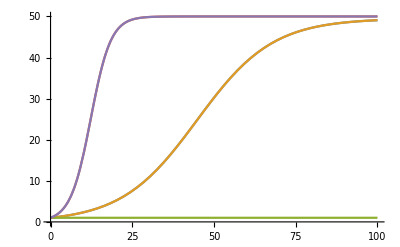

```mathematica
Plot[{vans,pans,cans,uans,lans},{t,0,100}]
```

Let’s consider the alternative:

```mathematica
LVaH1=v*Ha1*(1-((v+p+c)/K))
LVaH2=p*Ha2*(1-((v+p+c)/K))
LVaHG=c*HaG*(1-((v+p+c)/K))
LVaS1=u*Sa1*(1-((u+l)/K))
LVaS2=l*Sa2*(1-((u+l)/K))
```

v (1-(c+p+v)/K) (-s^2+s (l α γ+u α Γ))

p (1-(c+p+v)/K) (-s^2+s (u α γ+l α Γ))

c (1-(c+p+v)/K) (-g^2+g (l α+u α))

u (1-(l+u)/K) (c g (1-α)+p s (1-α) γ+s v (1-α) Γ)

l (1-(l+u)/K) (c g (1-α)+s v (1-α) γ+p s (1-α) Γ)

```mathematica
F[Γ_,α_ ,γ_,s_,g_,v0_,p0_,c0_,u0_,l0_,K_]:={v'[t]==v[t] (1-(c[t]+p[t]+v[t])/K) (-s^2+s (l[t] α γ+u[t] α Γ)),
p'[t]==p [t](1-(c[t]+p[t]+v[t])/K) (-s^2+s (u[t] α γ+l[t] α Γ)),
c'[t]==c [t](1-(c[t]+p[t]+v[t])/K) (-g^2+g (l[t] α+u [t]α)),
u'[t]==u[t] (1-(l[t]+u[t])/K) (c [t]g (1-α)+p[t] s (1-α) γ+s v [t](1-α) Γ),
l'[t]==l[t] (1-(l[t]+u[t])/K) (c[t] g (1-α)+s v[t] (1-α) γ+p [t]s (1-α) Γ),
v[0]==v0,p[0]==p0,c[0]==c0,u[0]==u0,l[0]==l0};
Numerica=F[2.2,0.5,0.5,0.5,0.5,1,1,1,1,1,100];
```

```mathematica
INT=NDSolve[Numerica, {v,p,c,u,l},{t,0,100}]
{vans,pans,cans,uans,lans}= {v[t],p[t],c[t],u[t],l[t]} /.Flatten[INT];
```

{{v→InterpolatingFunction[…],p→InterpolatingFunction[…],c→InterpolatingFunction[…],u→InterpolatingFunction[…],l→InterpolatingFunction[…]}}

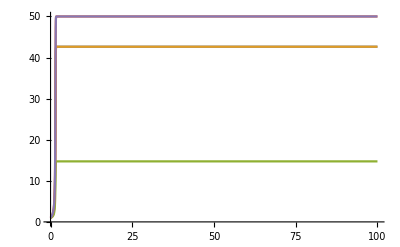

```mathematica
Plot[{vans,pans,cans,uans,lans},{t,0,100}]
```

Next well define this system a of lotka-Volterra equations:

```mathematica
COOPLVa={v (1-(c+p+v)/K) (-s^2+s ((l α γ)/(l+u)+(u α Γ)/(l+u))),p (1-(c+p+v)/K) (-s^2+s ((u α γ)/(l+u)+(l α Γ)/(l+u))),c (1-(c+p+v)/K) (-g^2+(g l α)/(l+u)+(u α)/(l+u)),u (1-(l+u)/K) ((c g (1-α))/(c+p+v)+(p s (1-α) γ)/(c+p+v)+(s v (1-α) Γ)/(c+p+v)),l (1-(l+u)/K) ((c g (1-α))/(c+p+v)+(s v (1-α) γ)/(c+p+v)+(p s (1-α) Γ)/(c+p+v))}//. {α-> 0.5,γ-> 0.5,Γ -> 2.2, g-> 0.5,s-> 0.5, K-> 100};
```

Next I grab the package I’ll need:

```mathematica
Get[NotebookDirectory[]<>"ReactionDiffusionLab.m"]
```

ok, got it!

Next We’ll define our initial conditions:

```mathematica
h=1/40;
v0=Table[RandomReal[],{y,0,1,h},{x,0,1,h}];
p0=Table[RandomReal[],{y,0,1,h},{x,0,1,h}];
c0=Table[RandomReal[],{y,0,1,h},{x,0,1,h}];
u0=Table[RandomReal[],{y,0,1,h},{x,0,1,h}];
l0=Table[RandomReal[],{y,0,1,h},{x,0,1,h}];
RDDensityPlots[{v0,p0,c0}, ImageSize -> Small]
```

Let’s give it a go I guess:

```mathematica
d1 = 0.000001;
d2 = 0.000001;
d3 = 0.000001;
d4=0.000001;
d5=0.000001;
```

```mathematica
Legended[RDDensityPlots[COOPLVa, {v,p,c,u,l}, {v0,p0,c0,u0,l0},{d1,d2,d3, d4,d5},{0,100,1}, ImageSize -> Large, PlotLegends -> Automatic, ColorFunction-> "BlueGreenYellow"],BarLegend[{"BlueGreenYellow",{0,1}},LegendLayout->"Column"]]
```

RDDensityPlots[{(-0.25+0.5 ((0.25 l)/(l+u)+(1.1 u)/(l+u))) (1+1/100 (-c-p-v)) v,p (-0.25+0.5 ((1.1 l)/(l+u)+(0.25 u)/(l+u))) (1+1/100 (-c-p-v)),c (-0.25+(0.25 l)/(l+u)+(0.5 u)/(l+u)) (1+1/100 (-c-p-v)),(1+1/100 (-l-u)) u ((0.25 c)/(c+p+v)+(0.125 p)/(c+p+v)+(0.55 v)/(c+p+v)),l (1+1/100 (-l-u)) ((0.25 c)/(c+p+v)+(0.55 p)/(c+p+v)+(0.125 v)/(c+p+v))},{v,p,c,u,l},{{{0.940021,0.0641434,0.144828,0.391822,0.157087,0.534069,0.22473,0.581707,0.747022,0.531917,0.337861,0.883296,0.525336,0.960709,0.834456,0.693984,0.580331,0.0474581,0.328801,0.692794,0.432118,0.995773,0.782623,0.33771,0.464849,0.862496,0.309795,0.712038,0.25025,0.383301,0.629711,0.440583,0.290005,0.719845,0.468434,0.781504,0.193284,0.915652,0.783262,0.866474,0.134894},{0.939883,0.603211,0.792338,0.440649,0.220656,0.902137,0.255072,0.130077,0.103562,0.164315,0.532148,0.413865,0.630721,0.20908,0.18716,0.564178,0.784172,0.821486,0.407374,0.379798,0.0849705,0.0739259,0.133974,0.796821,0.709582,0.891482,0.219342,0.199004,0.0828056,0.443034,0.18089,0.898761,0.55136,0.513619,0.509774,0.453507,0.982728,0.254791,0.0685268,0.0949511,0.732554},{0.00673339,0.185905,0.135365,0.620472,0.87861,0.955891,0.778758,0.253857,0.878779,0.3125,0.400259,0.118346,0.153473,0.150583,0.56415,0.484322,0.423077,0.50646,0.840538,0.787875,0.314336,0.118551,0.88794,0.363267,0.00369601,0.830249,0.862466,0.775841,0.720153,0.814042,0.924888,0.681579,0.438597,0.441649,0.0577367,0.615312,0.957472,0.0591955,0.400985,0.419687,0.312242},{0.291391,0.423081,0.436172,0.0660193,0.822975,0.466005,0.403277,0.458645,0.735594,0.783868,0.421319,0.905007,0.329428,0.142591,0.84297,0.911811,0.0650719,0.263046,0.201648,0.0697159,0.832986,0.590417,0.556396,0.00770525,0.369701,0.366657,0.417108,0.575753,0.0288963,0.792378,0.657788,0.871736,0.898661,0.0522483,0.912438,0.682343,0.596008,0.439975,0.590634,0.526071,0.579599},{0.504933,0.16858,0.994428,0.967039,0.770312,0.839841,0.69463,0.114004,0.649617,0.0911132,0.125487,0.656326,0.212557,0.224842,0.11981,0.885008,0.31818,0.265465,0.380457,0.904022,0.460313,0.110446,0.689228,0.954437,0.819973,0.919273,0.244243,0.885526,0.792146,0.645186,0.698712,0.344544,0.817959,0.595679,0.157754,0.120739,0.787324,0.17526,0.717905,0.192537,0.515551},{0.332928,0.515211,0.930027,0.217389,0.637566,0.110128,0.897979,0.426487,0.735207,0.732859,0.421861,0.984043,0.193325,0.797337,0.109633,0.523177,0.458244,0.145618,0.7857,0.491908,0.135558,0.830274,0.288591,0.053504,0.451415,0.653689,0.199366,0.289253,0.910277,0.545277,0.986225,0.0386957,0.234288,0.604662,0.641765,0.28023,0.282624,0.346487,0.826451,0.921515,0.750438},{0.253434,0.463251,0.138928,0.25934,0.765624,0.524636,0.61242,0.55742,0.140352,0.14973,0.9085,0.550791,0.253345,0.340297,0.188929,0.11456,0.0289102,0.204315,0.68962,0.122696,0.696977,0.290587,0.363903,0.405145,0.990586,0.767023,0.56104,0.943529,0.30543,0.119137,0.280268,0.439147,0.458531,0.284063,0.867479,0.985818,0.0566211,0.607416,0.638919,0.93319,0.99686},{0.167493,0.407839,0.967147,0.773502,0.375307,0.795849,0.0277082,0.406668,0.832934,0.287047,0.188354,0.991258,0.410557,0.135985,0.658419,0.237386,0.0110298,0.663813,0.155965,0.264557,0.583278,0.487195,0.843988,0.578628,0.0400186,0.369883,0.974264,0.263929,0.251834,0.348094,0.272193,0.679032,0.11333,0.378094,0.637736,0.264833,0.662842,0.504594,0.457065,0.69579,0.752545},{0.0896188,0.852273,0.0316635,0.00298251,0.0191011,0.992977,0.397327,0.655243,0.492115,0.793271,0.689605,0.737355,0.797472,0.115572,0.452929,0.467088,0.589467,0.0491272,0.743327,0.0338077,0.00739939,0.432777,0.652555,0.356766,0.240297,0.376033,0.680998,0.893761,0.203441,0.74487,0.651194,0.393977,0.557757,0.0249042,0.215663,0.987565,0.334602,0.451318,0.934724,0.522572,0.0961516},{0.663591,0.0300824,0.592014,0.272857,0.273525,0.697245,0.110674,0.427565,0.858197,0.0150414,0.334692,0.905876,0.391168,0.000491367,0.516498,0.728649,0.411498,0.594929,0.803279,0.518647,0.573013,0.255127,0.7282,0.420143,0.254513,0.136832,0.19702,0.595382,0.12306,0.202333,0.981984,0.765001,0.390343,0.288136,0.264016,0.897078,0.738078,0.544063,0.184359,0.466802,0.513563},{0.684389,0.19663,0.749521,0.150223,0.489523,0.90339,0.584556,0.242672,0.872118,0.381428,0.566518,0.00647378,0.42941,0.640017,0.906172,0.14873,0.355528,0.212658,0.940773,0.437767,0.393927,0.428704,0.64354,0.86022,0.211578,0.0158589,0.138098,0.562476,0.611644,0.412772,0.692009,0.439062,0.62435,0.268164,0.954193,0.446666,0.580554,0.413837,0.4972,0.470796,0.346192},{0.778285,0.0268383,0.983376,0.166459,0.538123,0.982355,0.0413433,0.749491,0.134186,0.734421,0.574239,0.288808,0.544488,0.881598,0.775818,0.73155,0.146912,0.704372,0.732046,0.0788461,0.68971,0.223274,0.324441,0.773116,0.592352,0.483852,0.267588,0.439921,0.223092,0.625342,0.976943,0.805218,0.297294,0.828293,0.389945,0.643289,0.0935683,0.33882,0.226424,0.650949,0.658576},{0.03666,0.233475,0.607817,0.891607,0.683825,0.690809,0.277036,0.957799,0.229682,0.0867835,0.571318,0.149428,0.821064,0.118304,0.0925698,0.794011,0.585359,0.596178,0.313128,0.945336,0.940269,0.479004,0.749734,0.902039,0.951783,0.432238,0.348427,0.788293,0.291987,0.714652,0.701267,0.704205,0.483186,0.121924,0.561176,0.673065,0.961042,0.991687,0.432309,0.595487,0.423013},{0.291747,0.498323,0.63231,0.748051,0.244059,0.43748,0.0795566,0.513284,0.368945,0.518897,0.886,0.0712945,0.476954,0.703989,0.10471,0.0880613,0.11621,0.586249,0.983833,0.48608,0.439953,0.139355,0.878196,0.536198,0.62408,0.00307668,0.347097,0.215445,0.346489,0.783716,0.901159,0.695955,0.0165103,0.0545632,0.0281333,0.840909,0.636128,0.28363,0.48398,0.728634,0.77727},{0.769418,0.886632,0.918625,0.439979,0.273448,0.882289,0.480738,0.260555,0.665619,0.478517,0.372246,0.240407,0.960931,0.953864,0.129816,0.581576,0.935241,0.326098,0.326591,0.769429,0.619469,0.811854,0.767985,0.28862,0.697873,0.639234,0.916111,0.983301,0.429972,0.401508,0.375038,0.204806,0.51346,0.0768317,0.982363,0.790285,0.968538,0.627516,0.82828,0.853232,0.301037},{0.480152,0.438756,0.614135,0.978286,0.0712798,0.379548,0.980199,0.267893,0.629085,0.507794,0.136958,0.405538,0.562157,0.868566,0.0900304,0.838291,0.209301,0.32508,0.23581,0.882379,0.547608,0.083027,0.21802,0.804058,0.98396,0.730372,0.0617185,0.937467,0.595233,0.340145,0.627158,0.915604,0.252428,0.290919,0.0138409,0.863563,0.407647,0.630257,0.266865,0.0805105,0.202797},{0.59536,0.55457,0.614263,0.814668,0.181056,0.580477,0.551707,0.52699,0.373564,0.687099,0.853555,0.0671185,0.647688,0.946235,0.0902846,0.587446,0.76063,0.161958,0.835646,0.826787,0.0892213,0.370517,0.154381,0.210771,0.333742,0.00120951,0.114759,0.120818,0.665893,0.960715,0.816359,0.168253,0.679069,0.746525,0.023676,0.592399,0.753363,0.809647,0.051982,0.880869,0.936024},{0.806386,0.872147,0.501094,0.264275,0.983102,0.531869,0.0049768,0.890159,0.665402,0.489234,0.670919,0.41372,0.55494,0.0634624,0.604738,0.0577003,0.11103,0.404214,0.728656,0.354,0.0615354,0.939872,0.0976284,0.124713,0.00328076,0.797509,0.451794,0.677293,0.460611,0.821405,0.188775,0.809349,0.626336,0.728554,0.219053,0.298562,0.664404,0.180412,0.801774,0.178175,0.891039},{0.117791,0.796112,0.11281,0.482088,0.241995,0.300703,0.839923,0.12196,0.947177,0.923845,0.705964,0.586644,0.545355,0.495462,0.47661,0.142881,0.950477,0.978754,0.420958,0.429954,0.267385,0.723475,0.81411,0.139514,0.425324,0.559288,0.0949575,0.113243,0.382781,0.679069,0.759708,0.222005,0.586635,0.752669,0.551666,0.595307,0.449591,0.6793,0.488511,0.770478,0.259954},{0.118165,0.890536,0.0433927,0.936869,0.0155824,0.455958,0.167649,0.370968,0.622343,0.686176,0.0505993,0.964847,0.785544,0.295855,0.85005,0.764739,0.946278,0.363867,0.0832969,0.266949,0.552506,0.462252,0.404777,0.303587,0.133391,0.0301666,0.163723,0.254633,0.773796,0.66522,0.426644,0.998719,0.432445,0.696418,0.405703,0.334651,0.656615,0.417621,0.685271,0.083497,0.585456},{0.464226,0.458706,0.883964,0.427512,0.705799,0.899793,0.510149,0.345338,0.593349,0.997029,0.514982,0.598907,0.121501,0.937497,0.96011,0.402278,0.129475,0.230638,0.0176892,0.666144,0.586313,0.223459,0.572323,0.335209,0.776158,0.815493,0.871287,0.679505,0.547959,0.55202,0.459643,0.402462,0.764215,0.0654474,0.534564,0.363431,0.288795,0.244414,0.960515,0.762425,0.493395},{0.798813,0.80402,0.183077,0.373197,0.992078,0.906135,0.265971,0.155831,0.663739,0.436502,0.791334,0.733875,0.359345,0.382731,0.836984,0.953754,0.542422,0.212031,0.64415,0.46209,0.631578,0.338193,0.962857,0.7227,0.981198,0.161595,0.784887,0.140702,0.659601,0.952532,0.682057,0.639956,0.0677428,0.172817,0.607642,0.302347,0.895182,0.102642,0.859301,0.55085,0.173589},{0.658605,0.148582,0.670801,0.0386649,0.779921,0.990689,0.38596,0.337887,0.0988497,0.855736,0.0321036,0.294577,0.28237,0.315697,0.083172,0.645497,0.435953,0.450851,0.862288,0.633207,0.261022,0.736312,0.603877,0.560304,0.208166,0.33492,0.755775,0.999594,0.366233,0.777884,0.634212,0.405565,0.151135,0.0703087,0.885881,0.962881,0.542572,0.988989,0.966677,0.65532,0.381823},{0.806854,0.113369,0.513425,0.9015,0.192558,0.753846,0.618751,0.897709,0.784761,0.730852,0.426518,0.290046,0.860849,0.613254,0.447387,0.405102,0.198568,0.693149,0.100614,0.969511,0.536505,0.365337,0.330798,0.969808,0.711426,0.32973,0.766051,0.899538,0.960029,0.919593,0.926457,0.743465,0.612896,0.374519,0.697143,0.322265,0.752228,0.107585,0.400576,0.324776,0.203135},{0.751222,0.547741,0.868991,0.47755,0.393084,0.119069,0.695777,0.626088,0.514142,0.270912,0.240016,0.918708,0.21934,0.419872,0.28708,0.281,0.26423,0.56586,0.36159,0.679191,0.25977,0.306205,0.771903,0.850218,0.354629,0.400225,0.115068,0.0947606,0.460989,0.578823,0.870094,0.0998163,0.110351,0.820211,0.895772,0.417518,0.22404,0.305631,0.0441803,0.082567,0.337927},{0.363246,0.0100094,0.0811633,0.105056,0.198257,0.358835,0.113328,0.321524,0.202099,0.379401,0.97188,0.731713,0.694236,0.447379,0.78097,0.537952,0.919758,0.793624,0.98949,0.801697,0.00548267,0.375238,0.269989,0.903727,0.667533,0.744991,0.0276353,0.792546,0.902642,0.0361911,0.92517,0.262574,0.845817,0.205632,0.210049,0.452296,0.363858,0.411846,0.150291,0.324521,0.728803},{0.293073,0.552305,0.0933946,0.0764926,0.155213,0.144587,0.657752,0.264121,0.853371,0.853794,0.915782,0.76598,0.721873,0.823303,0.911102,0.583636,0.867993,0.859101,0.680077,0.274811,0.279705,0.618474,0.595583,0.647588,0.570756,0.744992,0.405957,0.605262,0.873985,0.698031,0.758636,0.642131,0.383557,0.06952,0.872698,0.814656,0.951528,0.920687,0.660619,0.923687,0.965057},{0.326509,0.312623,0.0612859,0.0765998,0.513195,0.510326,0.301169,0.50082,0.409172,0.351014,0.0702777,0.959722,0.779394,0.0204164,0.656658,0.0804167,0.651304,0.661319,0.976467,0.647684,0.320788,0.0962747,0.650849,0.193697,0.360465,0.285162,0.186997,0.775127,0.0225388,0.973158,0.621297,0.920813,0.929229,0.399423,0.544029,0.492312,0.546068,0.652986,0.574695,0.183079,0.0682234},{0.851825,0.889183,0.509071,0.501872,0.657055,0.395555,0.477124,0.663445,0.889963,0.273019,0.120767,0.441215,0.474231,0.506069,0.416149,0.469223,0.493298,0.263875,0.457328,0.708814,0.120056,0.918592,0.860164,0.718838,0.82555,0.293225,0.429895,0.432296,0.656161,0.774072,0.277476,0.0932365,0.17258,0.085037,0.263056,0.406804,0.760322,0.510682,0.517268,0.331868,0.160721},{0.303881,0.39114,0.477268,0.43304,0.552263,0.424565,0.281546,0.636776,0.692931,0.768165,0.138545,0.30634,0.113086,0.870961,0.559442,0.632612,0.252922,0.268148,0.505602,0.906046,0.333875,0.417175,0.710157,0.938592,0.211588,0.533185,0.230998,0.828174,0.498561,0.650098,0.883227,0.849321,0.559199,0.230035,0.912917,0.980342,0.43168,0.209849,0.617988,0.267218,0.274046},{0.21909,0.365789,0.415914,0.789764,0.0115008,0.925602,0.565345,0.927533,0.0183107,0.0965898,0.0390502,0.46421,0.450785,0.00734532,0.135515,0.266517,0.608321,0.101365,0.830577,0.783924,0.564815,0.136407,0.580859,0.966494,0.24845,0.153156,0.453024,0.918321,0.558767,0.221233,0.806383,0.684267,0.245849,0.204737,0.56159,0.0130938,0.232179,0.342707,0.827917,0.271195,0.984412},{0.803964,0.300324,0.195644,0.720194,0.394657,0.0386315,0.0654755,0.927535,0.0443197,0.964568,0.401932,0.273261,0.501906,0.109877,0.499538,0.596873,0.658928,0.340806,0.866925,0.702483,0.87403,0.301666,0.952156,0.829467,0.0000316293,0.0497062,0.570181,0.595046,0.579397,0.148034,0.646654,0.168965,0.353211,0.527261,0.872653,0.621085,0.525722,0.128567,0.172646,0.255689,0.347547},{0.705184,0.97698,0.875492,0.198946,0.0839344,0.338751,0.285283,0.632672,0.379589,0.282963,0.101402,0.173626,0.367091,0.740915,0.793603,0.199369,0.853028,0.619227,0.515145,0.284,0.274042,0.509219,0.23283,0.736188,0.546637,0.153975,0.852796,0.761072,0.115993,0.667279,0.942863,0.513631,0.838636,0.323972,0.381962,0.667773,0.746133,0.855873,0.817489,0.0904826,0.271415},{0.766046,0.650872,0.707908,0.717056,0.949024,0.697584,0.102337,0.813707,0.0348164,0.314008,0.0396687,0.886192,0.268325,0.353948,0.726157,0.831693,0.0822797,0.716959,0.706354,0.658521,0.885025,0.945906,0.736074,0.405028,0.95204,0.280341,0.703096,0.529732,0.951932,0.168287,0.235291,0.690723,0.540398,0.251201,0.296766,0.629701,0.319178,0.628957,0.738897,0.226676,0.00657115},{0.722248,0.55621,0.153531,0.355638,0.189718,0.730956,0.582724,0.663912,0.633581,0.228119,0.847085,0.757714,0.313906,0.00611351,0.495659,0.993971,0.179874,0.753,0.354127,0.607143,0.68713,0.802367,0.944704,0.811411,0.303034,0.848356,0.541361,0.384625,0.339274,0.0170534,0.783904,0.787036,0.899057,0.636625,0.601903,0.300057,0.822434,0.344033,0.700896,0.32088,0.845234},{0.683571,0.472839,0.327086,0.84115,0.46431,0.605415,0.912504,0.829805,0.557145,0.191491,0.531839,0.978941,0.664334,0.760817,0.432352,0.32608,0.0327967,0.0885329,0.132171,0.332815,0.805921,0.339108,0.445582,0.24392,0.384829,0.869368,0.90178,0.37518,0.595852,0.435472,0.479597,0.347495,0.486614,0.947737,0.146281,0.630874,0.285102,0.921509,0.826257,0.933619,0.19149},{0.339152,0.17664,0.914019,0.329852,0.256335,0.900261,0.497686,0.945935,0.383114,0.245784,0.574414,0.956573,0.478241,0.967519,0.150429,0.749981,0.956385,0.372631,0.0879926,0.413029,0.0127158,0.898815,0.73524,0.350799,0.496692,0.839047,0.904019,0.93825,0.525256,0.271724,0.736017,0.728176,0.180032,0.945276,0.848288,0.78528,0.589946,0.0886129,0.358427,0.202652,0.486498},{0.0398333,0.406616,0.0715868,0.588795,0.958387,0.271094,0.790123,0.378543,0.625672,0.926733,0.463057,0.165683,0.000598225,0.347156,0.279127,0.0283899,0.101038,0.727098,0.388354,0.0282876,0.294128,0.756406,0.00327498,0.810295,0.596531,0.864294,0.722901,0.506305,0.31954,0.262525,0.666533,0.979955,0.611726,0.014661,0.239909,0.78908,0.985411,0.0247605,0.93905,0.9046,0.175276},{0.530603,0.866688,0.795222,0.466248,0.635507,0.0880177,0.337024,0.253925,0.998548,0.81804,0.27037,0.163018,0.0320263,0.940169,0.818967,0.500104,0.420148,0.736719,0.336882,0.51826,0.671335,0.608643,0.794378,0.00917003,0.281308,0.523241,0.160198,0.542784,0.661978,0.790794,0.592081,0.318174,0.240228,0.755975,0.422187,0.131194,0.552725,0.982958,0.70874,0.240773,0.071538},{0.229291,0.578094,0.179942,0.18266,0.436423,0.167192,0.366234,0.229345,0.713631,0.113965,0.909926,0.128386,0.409602,0.582023,0.907402,0.118914,0.451433,0.0911698,0.581011,0.59965,0.708715,0.686545,0.66847,0.182358,0.796972,0.347674,0.880703,0.124318,0.0682059,0.800021,0.875182,0.389048,0.158209,0.109412,0.368554,0.597348,0.991875,0.600374,0.104334,0.358639,0.623158},{0.869005,0.494783,0.723496,0.856615,0.571301,0.825487,0.466715,0.645234,0.591687,0.768852,0.182047,0.583577,0.0091117,0.497301,0.107348,0.980049,0.246728,0.330658,0.723161,0.28927,0.982332,0.0148638,0.841342,0.617118,0.870402,0.795111,0.61924,0.047854,0.506904,0.923903,0.00717869,0.499967,0.457202,0.150154,0.184345,0.578766,0.78425,0.399454,0.23447,0.778635,0.710589}},{{0.660308,0.846102,0.640798,0.647541,0.591821,0.289421,0.254638,0.963235,0.118913,0.801714,0.875333,0.174953,0.0977371,0.218643,0.0441455,0.0840924,0.635305,0.156364,0.57128,0.868863,0.467652,0.990091,0.359303,0.0901036,0.0799912,0.176039,0.861929,0.711907,0.956458,0.694088,0.92132,0.928183,0.288561,0.28938,0.899067,0.652281,0.476931,0.765252,0.717629,0.926821,0.543441},{0.239358,0.650232,0.395424,0.528591,0.214536,0.541757,0.108558,0.633193,0.165919,0.143578,0.137777,0.0192507,0.410436,0.983804,0.777154,0.320399,0.685021,0.64121,0.797007,0.302135,0.825757,0.529483,0.180565,0.56783,0.335973,0.138008,0.466567,0.250708,0.339339,0.683967,0.532711,0.661312,0.730214,0.490301,0.653617,0.334311,0.43583,0.801292,0.952134,0.634414,0.277908},{0.886863,0.862335,0.504148,0.606091,0.571451,0.540698,0.884117,0.273385,0.649155,0.0349493,0.791715,0.472571,0.167257,0.571055,0.355131,0.481691,0.609775,0.727218,0.407195,0.755211,0.185836,0.17886,0.906727,0.26461,0.829318,0.177084,0.698848,0.468853,0.878995,0.409166,0.307992,0.845801,0.201249,0.42476,0.814711,0.89362,0.634668,0.254005,0.237015,0.613118,0.0605649},{0.0738391,0.530234,0.743497,0.169927,0.592498,0.677361,0.127391,0.463714,0.0548295,0.124824,0.708065,0.101021,0.836678,0.107237,0.769268,0.83431,0.506191,0.242837,0.592435,0.0503715,0.296537,0.379142,0.426207,0.680439,0.295424,0.807148,0.107318,0.0384613,0.820475,0.995725,0.597958,0.757497,0.341079,0.204162,0.675847,0.624202,0.632048,0.85575,0.815528,0.859794,0.386678},{0.520745,0.967745,0.647713,0.6624,0.156322,0.476903,0.946418,0.953567,0.718079,0.785658,0.219525,0.483713,0.0294163,0.133208,0.379219,0.142901,0.19691,0.0203227,0.0874936,0.3618,0.0653266,0.394645,0.46235,0.0572243,0.800753,0.0826425,0.992922,0.0628211,0.982906,0.857157,0.58042,0.34562,0.659114,0.246621,0.196697,0.815266,0.67069,0.00588703,0.336703,0.86538,0.21786},{0.242841,0.798686,0.643635,0.519585,0.332168,0.0344001,0.408744,0.655828,0.529926,0.976792,0.941001,0.682757,0.198153,0.725605,0.688995,0.0401133,0.835997,0.648434,0.782077,0.584217,0.719277,0.426029,0.695903,0.757585,0.137874,0.303702,0.764931,0.250189,0.304925,0.504144,0.66714,0.100981,0.499102,0.458953,0.774359,0.0575891,0.00364725,0.0871444,0.846488,0.180197,0.7973},{0.90724,0.192225,0.0903099,0.557103,0.468012,0.451675,0.244324,0.0994048,0.51937,0.00855022,0.588654,0.386902,0.805302,0.780654,0.61611,0.96206,0.493025,0.0878852,0.528092,0.578838,0.981134,0.92316,0.79432,0.286788,0.971496,0.39229,0.359626,0.908676,0.00260424,0.255602,0.881808,0.867215,0.926949,0.946665,0.45551,0.956678,0.0128338,0.762653,0.99765,0.978864,0.0930498},{0.185671,0.388041,0.638911,0.495129,0.100094,0.605456,0.95651,0.278361,0.0979722,0.0529447,0.678349,0.471343,0.45276,0.488321,0.0185572,0.748203,0.701636,0.898195,0.186417,0.160685,0.524319,0.357607,0.24138,0.201649,0.479897,0.463832,0.746427,0.640199,0.43033,0.0381412,0.859351,0.806651,0.0573565,0.859194,0.0441183,0.783877,0.547582,0.737361,0.448358,0.196246,0.0468343},{0.800969,0.804473,0.327244,0.353092,0.387624,0.321371,0.47269,0.0114353,0.0631002,0.641958,0.362519,0.366352,0.502413,0.771386,0.572324,0.0238536,0.96601,0.101167,0.399378,0.159515,0.245666,0.573041,0.749571,0.646254,0.0584016,0.409089,0.542729,0.0332605,0.411423,0.986319,0.108412,0.899417,0.145715,0.176072,0.0166273,0.489237,0.897206,0.209129,0.759445,0.022807,0.446431},{0.0776704,0.86576,0.58637,0.149718,0.748231,0.117009,0.73136,0.034583,0.787095,0.615064,0.551109,0.858655,0.329388,0.854953,0.823579,0.611554,0.463214,0.282474,0.408071,0.0441134,0.924666,0.648718,0.529646,0.0237895,0.914797,0.0141418,0.13346,0.511886,0.604374,0.883754,0.659124,0.18753,0.745041,0.671356,0.633192,0.301883,0.0787004,0.957874,0.0264815,0.351044,0.642241},{0.27271,0.588507,0.910257,0.295579,0.61336,0.194918,0.764272,0.813806,0.265568,0.017583,0.106448,0.386134,0.884349,0.826855,0.26176,0.824257,0.579534,0.244665,0.350452,0.693459,0.444737,0.406673,0.484028,0.622385,0.0112966,0.0341058,0.910664,0.360526,0.412478,0.29041,0.332745,0.384295,0.247782,0.0386436,0.896857,0.895806,0.57511,0.409762,0.438141,0.523207,0.446999},{0.310941,0.223138,0.80865,0.779034,0.00447011,0.303157,0.452675,0.177783,0.925105,0.42023,0.952593,0.471918,0.244265,0.905247,0.577578,0.164911,0.682371,0.648919,0.283256,0.600729,0.570274,0.757877,0.869278,0.38827,0.116457,0.893867,0.99408,0.0307827,0.343642,0.150993,0.493017,0.397384,0.970926,0.227743,0.0576217,0.971733,0.553167,0.793387,0.190501,0.491077,0.600076},{0.904736,0.0656057,0.464473,0.552256,0.180442,0.750413,0.954391,0.331182,0.388724,0.866065,0.440292,0.334465,0.173847,0.826841,0.30882,0.428353,0.00152059,0.785393,0.335851,0.943095,0.463445,0.670034,0.71443,0.238244,0.240378,0.774112,0.918952,0.464662,0.0780339,0.958348,0.63558,0.238936,0.869655,0.925064,0.175048,0.442813,0.624895,0.449095,0.883518,0.575535,0.293843},{0.790094,0.455161,0.477069,0.72503,0.532822,0.0129528,0.775571,0.490909,0.354138,0.774844,0.315547,0.197474,0.703911,0.076687,0.605446,0.845738,0.426143,0.965675,0.606621,0.630866,0.629199,0.292033,0.566502,0.381444,0.0403563,0.0866056,0.875484,0.932703,0.952957,0.791494,0.376144,0.806115,0.748516,0.968656,0.363372,0.525101,0.252541,0.765628,0.105205,0.695977,0.186218},{0.208124,0.388956,0.622512,0.666473,0.113719,0.112379,0.85587,0.163508,0.713748,0.212648,0.216462,0.885546,0.490177,0.724537,0.553846,0.498686,0.170535,0.298394,0.927655,0.847898,0.464377,0.755653,0.0280832,0.251006,0.123853,0.092625,0.147025,0.67516,0.533344,0.727775,0.148759,0.582457,0.131417,0.731436,0.348318,0.553764,0.129161,0.884784,0.799846,0.70847,0.496335},{0.525888,0.417107,0.604962,0.568753,0.124489,0.388169,0.635473,0.0461542,0.223689,0.956351,0.44214,0.668835,0.247053,0.242832,0.97969,0.794847,0.38251,0.633533,0.751932,0.653266,0.223404,0.741156,0.665657,0.388972,0.522973,0.923401,0.583621,0.873203,0.79776,0.0463455,0.177735,0.449783,0.353879,0.187726,0.26725,0.339024,0.195816,0.385724,0.445875,0.923015,0.718257},{0.383273,0.628256,0.792405,0.915525,0.226817,0.318332,0.153421,0.929336,0.721526,0.940727,0.827525,0.0969914,0.652807,0.790424,0.789134,0.939082,0.649924,0.740697,0.278931,0.362552,0.340226,0.833866,0.721727,0.0582304,0.556013,0.945502,0.672867,0.992246,0.532303,0.325399,0.12055,0.925237,0.886934,0.616072,0.349934,0.547636,0.0795451,0.792595,0.727355,0.831753,0.364976},{0.167578,0.143214,0.776739,0.370746,0.213723,0.0921878,0.405656,0.368719,0.191971,0.407225,0.997769,0.80639,0.9686,0.60567,0.755181,0.313377,0.17191,0.436711,0.690513,0.602497,0.399433,0.42114,0.691013,0.0393093,0.128913,0.409373,0.490801,0.805484,0.185668,0.920498,0.568473,0.271996,0.408386,0.19131,0.985068,0.0994221,0.322388,0.897041,0.234741,0.568254,0.232667},{0.847859,0.804491,0.864015,0.330164,0.235628,0.836155,0.377956,0.672935,0.0731356,0.432205,0.333578,0.700266,0.0373164,0.737563,0.479908,0.604197,0.353095,0.211858,0.0760034,0.0497266,0.674467,0.119892,0.212073,0.490887,0.276293,0.0174056,0.037858,0.376561,0.741528,0.272936,0.715497,0.676172,0.994553,0.310641,0.660007,0.748954,0.397612,0.0798184,0.906053,0.926834,0.0253707},{0.462823,0.41989,0.286041,0.336363,0.490211,0.821464,0.573673,0.790856,0.540817,0.410721,0.0575223,0.905716,0.11959,0.429351,0.428929,0.454698,0.913573,0.447809,0.384719,0.841381,0.842275,0.895154,0.987624,0.246469,0.587824,0.383645,0.0130291,0.361977,0.645284,0.0505816,0.617496,0.861059,0.624419,0.152903,0.380078,0.669278,0.130462,0.262888,0.501215,0.716436,0.866624},{0.656565,0.582117,0.725934,0.579973,0.358759,0.698474,0.532806,0.429288,0.561324,0.529779,0.692155,0.113353,0.0645377,0.118938,0.605346,0.802553,0.168123,0.699521,0.743461,0.133923,0.375839,0.219607,0.989642,0.976697,0.648688,0.246329,0.669117,0.0034718,0.00130231,0.359725,0.529747,0.488791,0.516552,0.452293,0.930781,0.745728,0.596635,0.976005,0.548538,0.854415,0.86581},{0.688312,0.191634,0.966528,0.941497,0.572544,0.170858,0.621947,0.231732,0.838339,0.720129,0.666342,0.108282,0.230766,0.648525,0.509209,0.138235,0.73759,0.189583,0.752467,0.53759,0.0514504,0.83808,0.694655,0.129108,0.824003,0.321357,0.633636,0.568966,0.730217,0.39142,0.628118,0.721762,0.891677,0.684411,0.894685,0.916794,0.714456,0.953163,0.376322,0.740341,0.172283},{0.591293,0.902288,0.994517,0.959452,0.947986,0.250298,0.180775,0.510336,0.410179,0.986622,0.336284,0.756124,0.335557,0.3389,0.703843,0.194375,0.0719882,0.470085,0.301173,0.411837,0.87112,0.166034,0.438178,0.359583,0.495756,0.468575,0.649003,0.961745,0.559017,0.250659,0.78673,0.316125,0.454711,0.518403,0.606386,0.79846,0.527093,0.836679,0.551874,0.852021,0.917649},{0.287935,0.706887,0.997073,0.275971,0.503995,0.489658,0.382823,0.572912,0.295508,0.64381,0.575053,0.0274922,0.252235,0.977756,0.440774,0.475427,0.694517,0.660364,0.278207,0.58328,0.788278,0.773751,0.989331,0.318614,0.685632,0.853064,0.452625,0.577577,0.827147,0.892254,0.306386,0.483238,0.747626,0.46986,0.331991,0.620784,0.421012,0.500566,0.236707,0.218414,0.106843},{0.220312,0.998521,0.284942,0.27157,0.753184,0.865394,0.758977,0.383453,0.74819,0.300055,0.81145,0.218696,0.319293,0.921896,0.640995,0.745516,0.622914,0.0575237,0.539083,0.407847,0.554333,0.543689,0.699494,0.197616,0.87185,0.514443,0.138683,0.377682,0.734055,0.730828,0.52282,0.68271,0.934307,0.973287,0.575684,0.571602,0.634477,0.351207,0.977865,0.796898,0.367301},{0.264189,0.502131,0.605835,0.318536,0.123645,0.255847,0.372406,0.728065,0.273584,0.426815,0.580864,0.931825,0.693238,0.785603,0.780947,0.0154034,0.733222,0.29779,0.579978,0.382177,0.755086,0.642623,0.629762,0.480704,0.632776,0.60883,0.287574,0.0948918,0.003391,0.729398,0.989643,0.0185231,0.304765,0.674492,0.528611,0.116163,0.730638,0.4198,0.418058,0.249658,0.135938},{0.650833,0.323521,0.940638,0.0339477,0.137279,0.874537,0.305186,0.90089,0.328519,0.450204,0.698321,0.716196,0.0941258,0.0202014,0.272686,0.857919,0.775571,0.386506,0.833754,0.489683,0.519178,0.49812,0.438537,0.991035,0.466379,0.544063,0.895267,0.269838,0.497564,0.600536,0.979658,0.273903,0.080992,0.579482,0.152386,0.850312,0.706951,0.953285,0.47194,0.855174,0.423358},{0.559729,0.333073,0.943231,0.0966475,0.12355,0.0571081,0.839895,0.0900751,0.80723,0.954762,0.869788,0.590032,0.2679,0.394093,0.583009,0.900491,0.593213,0.191944,0.401678,0.163033,0.817881,0.600442,0.76844,0.631324,0.900402,0.990707,0.373624,0.447807,0.019665,0.0966506,0.947366,0.847407,0.333713,0.106892,0.352262,0.686065,0.960078,0.552479,0.483717,0.314906,0.747993},{0.242181,0.0460304,0.329295,0.0286841,0.648021,0.110593,0.322598,0.639836,0.21765,0.668741,0.402922,0.909929,0.367334,0.990276,0.771549,0.986889,0.536615,0.74076,0.104069,0.312494,0.556559,0.00517726,0.772051,0.350265,0.620721,0.821421,0.263457,0.153017,0.177438,0.871976,0.380141,0.40105,0.302973,0.782671,0.451864,0.320972,0.183542,0.189042,0.790147,0.102376,0.625148},{0.782423,0.916456,0.431164,0.450036,0.493446,0.210263,0.175575,0.177659,0.191399,0.332664,0.247714,0.334861,0.979641,0.27265,0.455945,0.434931,0.515174,0.596748,0.127044,0.824393,0.434331,0.853168,0.0824726,0.984987,0.60754,0.609191,0.703904,0.271945,0.546635,0.607822,0.777866,0.163319,0.151307,0.365997,0.892287,0.171235,0.671746,0.0597995,0.676192,0.499117,0.788197},{0.520692,0.515074,0.870555,0.632701,0.385147,0.330958,0.540429,0.387228,0.979696,0.391426,0.539665,0.0835939,0.293592,0.775844,0.277192,0.17893,0.122406,0.273877,0.127937,0.1049,0.189482,0.262141,0.239037,0.0833011,0.689672,0.8674,0.740837,0.212118,0.166787,0.150026,0.264446,0.10831,0.75958,0.588183,0.876746,0.170799,0.931658,0.266954,0.0422536,0.414491,0.170615},{0.19077,0.373329,0.418019,0.961351,0.221632,0.349514,0.165006,0.402158,0.716343,0.113339,0.823123,0.173446,0.826015,0.732022,0.778114,0.703166,0.29972,0.110646,0.748813,0.782042,0.999824,0.732486,0.101954,0.263675,0.619249,0.917994,0.237528,0.00890863,0.370829,0.682066,0.190405,0.863656,0.383044,0.521082,0.408639,0.735995,0.151418,0.0788423,0.433292,0.17051,0.650909},{0.800757,0.895436,0.51537,0.896251,0.371653,0.976079,0.513282,0.213506,0.10773,0.640395,0.189982,0.96075,0.591464,0.415019,0.821441,0.646383,0.00971954,0.81404,0.745936,0.853709,0.798701,0.132995,0.019395,0.782483,0.407424,0.0491827,0.495394,0.892219,0.561576,0.763714,0.447359,0.378087,0.18875,0.337442,0.45254,0.904353,0.500208,0.518881,0.556128,0.997077,0.143394},{0.0316177,0.399779,0.0321325,0.441468,0.657579,0.726634,0.0717595,0.988785,0.376511,0.427625,0.0848888,0.116129,0.236509,0.121685,0.672422,0.209608,0.694021,0.635636,0.535939,0.303681,0.0893097,0.879349,0.761492,0.255831,0.87451,0.396677,0.300047,0.211953,0.597925,0.233535,0.445784,0.556155,0.0103695,0.317189,0.915417,0.529824,0.642302,0.917716,0.277398,0.392137,0.840058},{0.199723,0.64769,0.984593,0.689042,0.0879672,0.66018,0.467392,0.613046,0.262438,0.2165,0.0356332,0.603132,0.598315,0.736162,0.396624,0.984786,0.386004,0.753148,0.552138,0.517829,0.94302,0.615378,0.278581,0.924943,0.9796,0.0786972,0.524842,0.652814,0.159115,0.528726,0.803158,0.862872,0.671379,0.395765,0.164646,0.839879,0.564769,0.2619,0.925126,0.77111,0.434029},{0.704023,0.646899,0.465578,0.336441,0.591218,0.698601,0.592159,0.244675,0.500652,0.40308,0.642963,0.414897,0.233742,0.202412,0.916698,0.204986,0.553309,0.117207,0.788432,0.308814,0.77916,0.486887,0.851874,0.0555749,0.869439,0.218462,0.664236,0.205556,0.372617,0.304195,0.466712,0.324527,0.555696,0.526993,0.382208,0.827064,0.58566,0.22138,0.191756,0.0857776,0.190164},{0.67982,0.487977,0.984654,0.0300838,0.0969491,0.440908,0.527578,0.131037,0.264581,0.348666,0.630008,0.742239,0.128009,0.54918,0.748203,0.567683,0.914314,0.423909,0.189337,0.36916,0.446761,0.800662,0.545234,0.0452676,0.255333,0.309529,0.770521,0.503962,0.756289,0.880308,0.612796,0.933765,0.296847,0.741115,0.89355,0.624916,0.623159,0.894531,0.861725,0.117058,0.89188},{0.317838,0.793506,0.530122,0.895438,0.761167,0.188894,0.206661,0.868581,0.512555,0.440552,0.580841,0.828598,0.286606,0.805444,0.1363,0.959458,0.174467,0.987585,0.0696484,0.216827,0.31083,0.554187,0.608639,0.560225,0.993298,0.0344094,0.664944,0.698351,0.753452,0.545216,0.9642,0.675987,0.76179,0.929578,0.147682,0.958603,0.0537464,0.928697,0.292585,0.813167,0.374259},{0.183448,0.384911,0.601276,0.539592,0.404228,0.22598,0.776987,0.938058,0.176851,0.0568532,0.921876,0.575457,0.130579,0.299553,0.877745,0.790403,0.7236,0.887975,0.129257,0.185072,0.771228,0.441604,0.825396,0.909563,0.0522343,0.0144477,0.541834,0.605921,0.555238,0.317759,0.815024,0.954509,0.344264,0.666568,0.198509,0.228002,0.97448,0.43472,0.503278,0.550957,0.492604},{0.834135,0.108256,0.904778,0.83298,0.85456,0.143383,0.286319,0.868351,0.771498,0.930746,0.708149,0.194587,0.773219,0.186627,0.95243,0.826523,0.434298,0.512843,0.830836,0.813533,0.0293372,0.346936,0.338666,0.169341,0.446372,0.545193,0.444146,0.875398,0.786524,0.0425777,0.76189,0.878922,0.825527,0.886997,0.345259,0.0725267,0.133498,0.554289,0.947272,0.495027,0.0258288},{0.544956,0.46431,0.993661,0.103052,0.928489,0.151784,0.796224,0.192351,0.105328,0.699916,0.998476,0.477333,0.320613,0.291281,0.191475,0.278778,0.892899,0.512855,0.567157,0.502719,0.253616,0.867592,0.492434,0.229685,0.0448188,0.743262,0.733794,0.819683,0.83809,0.772294,0.0959219,0.103111,0.969596,0.724654,0.611627,0.501884,0.919383,0.011932,0.29036,0.298415,0.187774}},{{0.190544,0.514797,0.493721,0.481916,0.640598,0.742476,0.213904,0.286112,0.366206,0.613987,0.498993,0.0870422,0.84321,0.155639,0.490182,0.0904117,0.529631,0.741048,0.316355,0.169124,0.209788,0.0729108,0.154616,0.934062,0.629334,0.25019,0.0529219,0.1513,0.696743,0.165508,0.873679,0.255328,0.158341,0.1095,0.688797,0.222351,0.45335,0.337668,0.979494,0.348866,0.845263},{0.646924,0.854878,0.461933,0.151649,0.0934206,0.559342,0.660893,0.302461,0.92707,0.0815435,0.489905,0.631392,0.216572,0.959891,0.471998,0.163613,0.0906753,0.654826,0.102052,0.0570197,0.934414,0.206703,0.34854,0.929397,0.800202,0.373097,0.425644,0.782673,0.577656,0.474307,0.801951,0.683196,0.408232,0.854977,0.612034,0.781768,0.269756,0.590968,0.674669,0.196632,0.188483},{0.415056,0.813185,0.226959,0.762926,0.279059,0.440425,0.347094,0.361447,0.973177,0.22679,0.296986,0.471155,0.144638,0.378881,0.897341,0.400715,0.135441,0.118465,0.460317,0.0683462,0.496702,0.729472,0.50587,0.0141868,0.102632,0.391877,0.781292,0.58334,0.0207126,0.622372,0.511752,0.0620838,0.383344,0.785881,0.40369,0.795492,0.170317,0.532983,0.611761,0.706308,0.228345},{0.981163,0.41455,0.921892,0.513383,0.0672683,0.858563,0.461251,0.317862,0.468396,0.765426,0.581099,0.281453,0.133137,0.945466,0.0797856,0.772792,0.542313,0.592532,0.403966,0.545423,0.492067,0.991871,0.640244,0.373169,0.689945,0.319015,0.758642,0.0513892,0.90855,0.253006,0.772974,0.688206,0.104071,0.242546,0.196314,0.049805,0.631548,0.93777,0.793812,0.733792,0.191969},{0.851023,0.0754014,0.246281,0.610213,0.878283,0.805603,0.0914836,0.0535527,0.0590636,0.666131,0.667246,0.775852,0.967375,0.326642,0.93452,0.45538,0.863549,0.435396,0.451275,0.699707,0.858175,0.769516,0.542664,0.384012,0.586341,0.0747489,0.0256288,0.514576,0.373837,0.96482,0.356373,0.73839,0.0518813,0.546865,0.29675,0.48893,0.188661,0.582439,0.139305,0.687093,0.135088},{0.373582,0.665732,0.323794,0.517347,0.285973,0.306078,0.813292,0.265958,0.456741,0.502059,0.416065,0.422246,0.408527,0.0753455,0.0647529,0.650602,0.292789,0.680862,0.455649,0.987553,0.722986,0.262114,0.950778,0.729937,0.107904,0.540349,0.249908,0.0470359,0.654641,0.303205,0.555022,0.802722,0.0216993,0.163798,0.848461,0.548479,0.324074,0.34848,0.702205,0.38364,0.0169317},{0.716859,0.368839,0.460555,0.978291,0.359072,0.49941,0.363094,0.560763,0.958133,0.372858,0.716789,0.189358,0.266416,0.152239,0.928131,0.761315,0.438688,0.532184,0.897538,0.0367581,0.920701,0.997791,0.308034,0.360522,0.15074,0.536951,0.500862,0.387862,0.537178,0.0542407,0.650733,0.868743,0.0712369,0.81475,0.437255,0.615267,0.3551,0.941253,0.104786,0.512391,0.881112},{0.194274,0.0273084,0.0286015,0.463421,0.0845781,0.1303,0.952245,0.237988,0.57744,0.413757,0.827216,0.242285,0.314579,0.650781,0.997807,0.357735,0.845534,0.341009,0.359084,0.00914449,0.703125,0.828842,0.773377,0.569072,0.200441,0.394977,0.535863,0.8052,0.771531,0.85368,0.116702,0.00533538,0.141221,0.424809,0.450367,0.446161,0.305787,0.737588,0.388205,0.226986,0.273503},{0.596733,0.558868,0.19957,0.889387,0.611241,0.901444,0.164818,0.335323,0.312972,0.971895,0.464337,0.772667,0.84679,0.913565,0.826898,0.15299,0.609619,0.0717523,0.944439,0.292335,0.635439,0.775187,0.430317,0.696743,0.209882,0.349117,0.382693,0.738649,0.541818,0.629409,0.0409986,0.913243,0.593478,0.863263,0.457091,0.808043,0.700968,0.69805,0.430499,0.394124,0.783822},{0.915014,0.966377,0.377834,0.34044,0.725043,0.796826,0.505185,0.323061,0.019489,0.0387663,0.540764,0.0967223,0.281756,0.161749,0.551131,0.613085,0.010641,0.241442,0.759232,0.72912,0.00300014,0.67226,0.641625,0.44493,0.627089,0.565311,0.152914,0.558192,0.93998,0.583799,0.694503,0.133319,0.33838,0.094954,0.772921,0.412808,0.654576,0.800127,0.362581,0.267845,0.577614},{0.558883,0.0986844,0.891862,0.179417,0.379584,0.114973,0.471224,0.294785,0.807566,0.197247,0.953192,0.528468,0.446851,0.83807,0.0453324,0.352317,0.982501,0.191817,0.107849,0.979553,0.170474,0.206042,0.202968,0.971718,0.527667,0.34081,0.154413,0.27381,0.349305,0.757648,0.847447,0.661054,0.0895994,0.701655,0.0929905,0.0540422,0.110721,0.643855,0.113208,0.306469,0.709692},{0.908874,0.601393,0.900054,0.656758,0.722064,0.227255,0.724017,0.460251,0.0959669,0.00875411,0.803175,0.436078,0.0258154,0.0426883,0.935527,0.447889,0.563971,0.399294,0.273763,0.339059,0.554228,0.435423,0.941582,0.327691,0.300387,0.88107,0.329474,0.721455,0.376971,0.306719,0.921838,0.870068,0.26112,0.676077,0.120559,0.578678,0.715766,0.673076,0.990343,0.706704,0.308803},{0.410184,0.818594,0.246589,0.283218,0.902031,0.801107,0.696424,0.584312,0.709366,0.372402,0.781006,0.92985,0.326539,0.894396,0.808338,0.864437,0.966229,0.474612,0.92878,0.740222,0.156606,0.385938,0.086781,0.723961,0.860047,0.90922,0.91923,0.32093,0.549742,0.290854,0.993057,0.664553,0.48563,0.943027,0.919536,0.30568,0.289848,0.788466,0.908896,0.682631,0.673905},{0.692423,0.648965,0.173594,0.923245,0.275559,0.711584,0.0682244,0.4225,0.376086,0.926126,0.478517,0.0916618,0.341069,0.444006,0.0517784,0.0382894,0.482775,0.551878,0.588488,0.0491246,0.0779745,0.0499938,0.702382,0.129465,0.839537,0.38405,0.998829,0.170169,0.382911,0.902639,0.0849096,0.193143,0.254098,0.391075,0.831661,0.865597,0.262864,0.603704,0.248653,0.0143096,0.500455},{0.790878,0.878667,0.424679,0.76332,0.302385,0.759876,0.40835,0.961866,0.583207,0.408707,0.460551,0.0351901,0.748333,0.282857,0.614248,0.804213,0.964988,0.528083,0.974719,0.647164,0.748623,0.385262,0.42759,0.586548,0.131452,0.587914,0.775074,0.918694,0.105742,0.509928,0.124865,0.454637,0.761347,0.531977,0.993485,0.860947,0.164782,0.45361,0.342855,0.521688,0.286156},{0.153847,0.076793,0.399157,0.356514,0.18792,0.748889,0.937783,0.569307,0.372409,0.990719,0.363259,0.159533,0.594014,0.0410185,0.926966,0.631492,0.984319,0.180169,0.559009,0.36131,0.440017,0.363954,0.958548,0.439923,0.211657,0.815729,0.180686,0.743647,0.523501,0.635036,0.0576025,0.606345,0.14373,0.0421533,0.0380345,0.949578,0.5612,0.351525,0.999908,0.343149,0.864333},{0.450138,0.566414,0.55925,0.0745284,0.292541,0.721944,0.971641,0.0852167,0.432857,0.727961,0.246144,0.681997,0.44966,0.460676,0.380352,0.298183,0.471699,0.837041,0.77161,0.766625,0.389368,0.070783,0.0301263,0.231548,0.811908,0.473627,0.0761506,0.916423,0.656231,0.554802,0.482077,0.202176,0.865564,0.0264043,0.267692,0.0339111,0.917663,0.609534,0.0193996,0.845033,0.0724202},{0.463675,0.317687,0.467047,0.161092,0.800753,0.45964,0.662777,0.454939,0.0920206,0.348057,0.914093,0.433406,0.798364,0.531166,0.259516,0.201341,0.276329,0.485198,0.323379,0.686108,0.670694,0.968893,0.393775,0.231766,0.90828,0.772397,0.978237,0.857784,0.082375,0.828029,0.963054,0.767232,0.0655737,0.345752,0.272139,0.486042,0.542859,0.119944,0.857191,0.00960913,0.475681},{0.982413,0.812144,0.39934,0.323764,0.586053,0.843565,0.351822,0.12029,0.153232,0.923717,0.698166,0.612159,0.731876,0.32043,0.925476,0.671508,0.570379,0.0705674,0.421931,0.683866,0.756969,0.218133,0.28141,0.0479332,0.680146,0.42937,0.0146074,0.875513,0.908469,0.975766,0.697027,0.699138,0.023683,0.338451,0.66353,0.0718097,0.153598,0.199418,0.935617,0.351721,0.984517},{0.798627,0.965398,0.298131,0.816418,0.950052,0.347236,0.00868467,0.44204,0.352668,0.187805,0.00887136,0.828719,0.492954,0.572938,0.900514,0.161084,0.748332,0.343577,0.311572,0.896009,0.549549,0.231439,0.84452,0.287899,0.455264,0.38433,0.692184,0.0370261,0.338137,0.860341,0.627677,0.718368,0.481815,0.464795,0.526315,0.113698,0.70204,0.4429,0.0960568,0.441753,0.350714},{0.813891,0.513444,0.264486,0.860736,0.653432,0.495123,0.168725,0.260386,0.689945,0.427549,0.286464,0.818351,0.235327,0.280274,0.571227,0.995999,0.430863,0.307331,0.864108,0.0628775,0.393492,0.106796,0.260121,0.00214868,0.833028,0.804723,0.384882,0.427889,0.378716,0.0353377,0.752669,0.663291,0.462044,0.208266,0.40476,0.455696,0.981861,0.611357,0.651648,0.33865,0.689589},{0.435998,0.637803,0.419208,0.311177,0.0543718,0.162777,0.286119,0.678685,0.240365,0.422134,0.0956252,0.967711,0.37583,0.743749,0.843146,0.923346,0.630792,0.32088,0.0858298,0.555022,0.602931,0.782531,0.0916916,0.393173,0.877582,0.660519,0.919332,0.511239,0.821297,0.0655317,0.486057,0.0020262,0.14334,0.266786,0.593208,0.89129,0.410134,0.817794,0.71414,0.287468,0.195841},{0.475355,0.395376,0.350949,0.87907,0.500765,0.608187,0.886839,0.540491,0.793768,0.364627,0.457757,0.816925,0.447024,0.66195,0.701458,0.415205,0.719465,0.688761,0.813982,0.732799,0.521956,0.0807013,0.0381969,0.744304,0.743992,0.719375,0.610014,0.840635,0.204963,0.967197,0.93556,0.00752917,0.656935,0.592796,0.538799,0.10218,0.606543,0.476704,0.535105,0.837927,0.240031},{0.868747,0.774696,0.854799,0.470406,0.0433268,0.760477,0.765546,0.49628,0.228547,0.0385897,0.715334,0.310323,0.958361,0.19656,0.667498,0.783994,0.482338,0.403074,0.783162,0.50673,0.713922,0.713205,0.379985,0.9117,0.790293,0.732187,0.952691,0.813258,0.55901,0.307903,0.337452,0.0557205,0.00536214,0.175431,0.255522,0.028805,0.599538,0.537005,0.877843,0.433298,0.184364},{0.904801,0.0576774,0.041536,0.643314,0.646549,0.494286,0.973181,0.697997,0.534977,0.446793,0.5776,0.477067,0.477922,0.999633,0.978841,0.934646,0.23649,0.377238,0.337038,0.132373,0.0568889,0.585278,0.83689,0.728967,0.900469,0.83058,0.441224,0.140766,0.694761,0.611861,0.00771283,0.378836,0.295498,0.251858,0.0560365,0.484911,0.24736,0.742509,0.299112,0.552602,0.992122},{0.711286,0.446491,0.830215,0.310167,0.153847,0.5985,0.794113,0.494697,0.497996,0.532653,0.453367,0.185886,0.370051,0.0247544,0.541437,0.737961,0.0135872,0.232295,0.724059,0.156173,0.56296,0.456398,0.0432315,0.380411,0.193131,0.664593,0.946605,0.834825,0.941472,0.487077,0.342858,0.52441,0.0558377,0.750668,0.334241,0.0206421,0.782809,0.745327,0.279404,0.543984,0.126417},{0.519979,0.26423,0.114704,0.214653,0.768495,0.281109,0.159911,0.685994,0.94703,0.397543,0.409519,0.579062,0.0115168,0.332915,0.135428,0.968198,0.0368277,0.901003,0.707357,0.892919,0.165524,0.437444,0.461578,0.753233,0.165675,0.153405,0.377812,0.990604,0.600276,0.632124,0.418652,0.667541,0.161252,0.278852,0.825565,0.138551,0.288316,0.0508258,0.216235,0.787611,0.59605},{0.201672,0.574107,0.0777262,0.341519,0.783242,0.587386,0.690897,0.902604,0.116689,0.646048,0.602982,0.0552084,0.58158,0.238617,0.367242,0.559654,0.273857,0.557029,0.420883,0.869005,0.210022,0.758481,0.62339,0.105409,0.901971,0.0843846,0.49321,0.581265,0.634396,0.777923,0.679368,0.331619,0.733703,0.392556,0.120227,0.0442832,0.5186,0.739888,0.640786,0.143989,0.36491},{0.128228,0.341587,0.704768,0.606178,0.863069,0.570669,0.347038,0.677285,0.676485,0.291759,0.809312,0.766965,0.637014,0.362074,0.272228,0.85536,0.69072,0.910367,0.948856,0.393139,0.745593,0.417551,0.125523,0.386274,0.739433,0.16868,0.447574,0.968293,0.123636,0.821048,0.720927,0.827372,0.964838,0.797581,0.68185,0.363772,0.239596,0.400956,0.336853,0.655001,0.116674},{0.720601,0.997876,0.488697,0.475831,0.826346,0.611704,0.346852,0.504744,0.20296,0.922559,0.413937,0.898362,0.453427,0.246538,0.655308,0.595567,0.43259,0.908306,0.0206603,0.369399,0.713976,0.802618,0.171962,0.698833,0.2441,0.222818,0.950531,0.927213,0.881599,0.793548,0.217537,0.235341,0.151467,0.0129313,0.688984,0.123472,0.139536,0.381823,0.308436,0.86427,0.822229},{0.060207,0.627864,0.135116,0.0522897,0.881093,0.727084,0.974427,0.788426,0.90541,0.962992,0.832778,0.72871,0.0598386,0.391131,0.759325,0.591055,0.930208,0.674393,0.654516,0.856276,0.832509,0.192711,0.605736,0.221143,0.0047351,0.508514,0.0292783,0.665831,0.390947,0.386545,0.221772,0.991472,0.351747,0.13793,0.451599,0.826893,0.200783,0.953408,0.793857,0.701158,0.69886},{0.397433,0.759279,0.33325,0.0740315,0.78607,0.512766,0.546198,0.693361,0.575569,0.294992,0.43506,0.400273,0.609088,0.193712,0.803972,0.298018,0.827904,0.79308,0.282293,0.428532,0.784794,0.058995,0.986454,0.353046,0.59825,0.115628,0.409843,0.341587,0.226156,0.35544,0.463616,0.502946,0.332203,0.386565,0.623495,0.516084,0.3532,0.286184,0.992425,0.41961,0.882618},{0.691785,0.168487,0.564125,0.14129,0.585277,0.12019,0.786125,0.398092,0.23549,0.824939,0.735097,0.437341,0.442986,0.942709,0.859825,0.735942,0.22725,0.0402879,0.0182028,0.53377,0.588244,0.544502,0.583877,0.112017,0.571048,0.791914,0.927816,0.794467,0.490874,0.87067,0.612494,0.922233,0.72925,0.698857,0.979753,0.586579,0.791349,0.342491,0.911073,0.143811,0.222441},{0.541338,0.945954,0.256511,0.904433,0.300995,0.506687,0.220454,0.35433,0.887417,0.20315,0.439971,0.712979,0.348838,0.648002,0.286779,0.441365,0.482456,0.262489,0.466025,0.375107,0.506942,0.815078,0.904698,0.110913,0.299427,0.804377,0.433947,0.0827354,0.941875,0.0144857,0.962335,0.577829,0.851375,0.425886,0.784508,0.173589,0.0443044,0.802963,0.609494,0.719387,0.724611},{0.528814,0.368612,0.780296,0.716603,0.0959618,0.700506,0.183511,0.583937,0.0158597,0.0776583,0.953116,0.637698,0.543957,0.135752,0.818724,0.78516,0.139421,0.425296,0.854103,0.257536,0.688538,0.919673,0.11706,0.0822088,0.356722,0.465884,0.818533,0.228549,0.686013,0.851553,0.0268402,0.831042,0.553557,0.219715,0.302825,0.727258,0.450521,0.674449,0.351176,0.0653243,0.274127},{0.875442,0.399819,0.327506,0.239834,0.151117,0.468305,0.351181,0.0900446,0.92222,0.926492,0.255488,0.915724,0.544748,0.586027,0.41655,0.798654,0.383797,0.198087,0.153427,0.622173,0.694397,0.404262,0.833415,0.920937,0.128605,0.161835,0.309622,0.802617,0.362313,0.632681,0.885436,0.861708,0.590649,0.232507,0.0151329,0.885671,0.460039,0.854186,0.377017,0.921257,0.200982},{0.473436,0.182788,0.218201,0.854063,0.598702,0.165863,0.361016,0.366969,0.214854,0.784174,0.335847,0.373776,0.800554,0.0396333,0.522904,0.311622,0.609767,0.100581,0.507134,0.369767,0.659557,0.271001,0.461388,0.0276738,0.0961591,0.0151846,0.65187,0.144212,0.441435,0.956829,0.0677235,0.1926,0.858637,0.926203,0.449374,0.204136,0.169899,0.0701012,0.734416,0.769071,0.691536},{0.181721,0.290031,0.139716,0.52165,0.282231,0.969368,0.560748,0.195104,0.785843,0.181466,0.498916,0.664962,0.0758455,0.454063,0.841802,0.458372,0.893676,0.205909,0.182786,0.8907,0.0249887,0.377727,0.552655,0.197186,0.557718,0.000897105,0.311883,0.617902,0.176576,0.742778,0.83042,0.0582135,0.287671,0.917829,0.73874,0.701418,0.0847436,0.709664,0.0677652,0.128842,0.384652},{0.245884,0.0716234,0.167393,0.175539,0.923987,0.739049,0.318558,0.478505,0.910388,0.409351,0.778862,0.139196,0.350712,0.689103,0.807843,0.0608477,0.36906,0.721213,0.322295,0.0915665,0.811322,0.598534,0.507251,0.314741,0.284036,0.969026,0.647758,0.104725,0.852671,0.6678,0.773469,0.213338,0.823566,0.720575,0.559655,0.458948,0.229432,0.56008,0.448197,0.511131,0.356326},{0.478386,0.15187,0.778915,0.118278,0.38574,0.738121,0.231083,0.568192,0.101993,0.576213,0.475527,0.149707,0.991843,0.558245,0.923446,0.022699,0.55037,0.977188,0.591072,0.554742,0.194143,0.651123,0.321319,0.334549,0.606992,0.992063,0.533664,0.326776,0.416134,0.137522,0.873703,0.591447,0.603518,0.00205557,0.184829,0.191145,0.290709,0.0525877,0.627459,0.193441,0.703939},{0.665237,0.617901,0.872731,0.59737,0.385898,0.7268,0.623476,0.297573,0.382615,0.106683,0.591739,0.357146,0.302546,0.190859,0.954967,0.338101,0.470274,0.467334,0.307622,0.310288,0.433156,0.532937,0.123321,0.658254,0.679641,0.129265,0.232763,0.660515,0.610066,0.247655,0.78492,0.550384,0.962381,0.786989,0.357824,0.516505,0.946227,0.716592,0.437076,0.380223,0.0651632}},{{0.867756,0.826813,0.434395,0.173439,0.166398,0.921339,0.443935,0.874022,0.54555,0.270558,0.760688,0.592999,0.794811,0.892163,0.943085,0.0211694,0.204973,0.292833,0.971368,0.0149749,0.569105,0.563197,0.44318,0.0583493,0.202199,0.866269,0.81005,0.264765,0.743597,0.0824218,0.651664,0.327435,0.945301,0.542826,0.539977,0.139299,0.562841,0.827531,0.643643,0.0538287,0.338897},{0.767336,0.0719961,0.827652,0.554838,0.914792,0.40308,0.822351,0.920198,0.82899,0.736422,0.372266,0.143976,0.341455,0.792856,0.150424,0.26697,0.135083,0.721032,0.172543,0.681163,0.708755,0.972437,0.310273,0.337736,0.00722037,0.978976,0.0352544,0.0625039,0.0298633,0.29992,0.157784,0.447058,0.897438,0.749594,0.191027,0.582639,0.184669,0.0237708,0.0447088,0.227129,0.989253},{0.410156,0.608386,0.738533,0.0944816,0.234191,0.490535,0.605111,0.464408,0.723436,0.54397,0.181782,0.307825,0.532146,0.877104,0.0379217,0.960502,0.212869,0.966812,0.791218,0.900275,0.067289,0.352234,0.216597,0.1795,0.731963,0.112379,0.924762,0.400587,0.724402,0.382146,0.678726,0.908773,0.625348,0.507571,0.674587,0.615806,0.634845,0.723099,0.98269,0.507344,0.246683},{0.0598661,0.74645,0.362497,0.429115,0.628674,0.86246,0.0393732,0.833596,0.674741,0.926358,0.171204,0.988185,0.803548,0.551591,0.307585,0.176181,0.159705,0.0482186,0.844059,0.153871,0.125594,0.039993,0.573068,0.229339,0.0341619,0.936677,0.668418,0.954251,0.653476,0.152941,0.571336,0.00593078,0.566236,0.363187,0.437231,0.193728,0.688834,0.452865,0.588565,0.0932158,0.45673},{0.798849,0.438323,0.814478,0.24527,0.234786,0.83965,0.849884,0.964861,0.400654,0.123324,0.97196,0.17728,0.238485,0.345356,0.972581,0.901376,0.7536,0.363116,0.48598,0.60809,0.469917,0.833422,0.617953,0.96939,0.586921,0.873974,0.593598,0.127291,0.86246,0.224067,0.362958,0.0464431,0.0525813,0.67317,0.815053,0.948119,0.593172,0.277394,0.682555,0.201598,0.489448},{0.406902,0.279993,0.957602,0.375621,0.546587,0.270812,0.106768,0.989456,0.546717,0.279985,0.342577,0.269255,0.775175,0.558472,0.72803,0.579367,0.711934,0.385075,0.206244,0.704796,0.0727346,0.0588412,0.501786,0.666939,0.362003,0.186723,0.635165,0.0178834,0.867492,0.77639,0.819225,0.675371,0.136154,0.603198,0.761088,0.735439,0.280809,0.096317,0.128796,0.257218,0.219557},{0.043902,0.369256,0.474471,0.928813,0.0624097,0.680052,0.987872,0.591946,0.844374,0.0712089,0.938537,0.728693,0.673528,0.236776,0.245556,0.48871,0.379706,0.0731751,0.969914,0.929633,0.656823,0.513589,0.797406,0.234053,0.792108,0.0203245,0.665495,0.0160624,0.243889,0.495972,0.162398,0.723082,0.254891,0.542912,0.144361,0.76165,0.357373,0.224354,0.266664,0.450112,0.240099},{0.267724,0.0592186,0.150983,0.0527314,0.0705535,0.188993,0.495513,0.753638,0.696511,0.518283,0.864189,0.544819,0.395772,0.0313146,0.199015,0.600081,0.19207,0.716302,0.0156049,0.689316,0.638956,0.974501,0.302199,0.735745,0.545125,0.192639,0.280267,0.746074,0.0500911,0.316097,0.980638,0.847462,0.0865242,0.453171,0.821963,0.823782,0.166395,0.150433,0.169856,0.825137,0.461068},{0.831211,0.662898,0.470413,0.441489,0.816865,0.853917,0.906938,0.556706,0.85812,0.185086,0.90835,0.356375,0.60622,0.399987,0.456377,0.507595,0.468319,0.868616,0.0675095,0.279072,0.116013,0.481981,0.208309,0.560922,0.294255,0.35114,0.471096,0.884593,0.770102,0.827519,0.172826,0.265429,0.551621,0.634327,0.781997,0.559229,0.494492,0.447948,0.640389,0.144302,0.42463},{0.543284,0.298627,0.746701,0.838002,0.751973,0.0543892,0.738369,0.915476,0.012714,0.0241192,0.548764,0.866159,0.507257,0.0329289,0.545911,0.404973,0.666372,0.605481,0.672888,0.545018,0.325968,0.582573,0.248273,0.220451,0.909847,0.846221,0.563779,0.820795,0.211777,0.911851,0.712731,0.0237256,0.611234,0.391552,0.0965431,0.0499415,0.102645,0.51546,0.253649,0.759811,0.808331},{0.592576,0.748554,0.392273,0.588386,0.934609,0.97958,0.390618,0.246114,0.887321,0.51087,0.767391,0.972571,0.0292724,0.136056,0.682145,0.483733,0.19807,0.950172,0.542375,0.603394,0.956493,0.288966,0.724831,0.909645,0.836009,0.518244,0.218081,0.897229,0.552094,0.68416,0.459746,0.372293,0.210344,0.546723,0.731582,0.00893797,0.612038,0.792727,0.973569,0.963133,0.0511101},{0.988397,0.189569,0.0296389,0.753566,0.0834889,0.662168,0.643219,0.519393,0.575357,0.971008,0.0279075,0.916817,0.636177,0.871312,0.635954,0.975355,0.865002,0.000208199,0.705333,0.545862,0.851834,0.613399,0.880701,0.133018,0.993226,0.0412216,0.330488,0.0839519,0.735464,0.802494,0.514739,0.811611,0.630483,0.131857,0.0135228,0.960069,0.0951477,0.113225,0.855393,0.332954,0.993158},{0.590319,0.334991,0.189834,0.975789,0.0996036,0.406677,0.333635,0.92528,0.273505,0.3659,0.606203,0.330371,0.784637,0.165555,0.807591,0.297026,0.291631,0.371316,0.413647,0.445783,0.870371,0.771961,0.231771,0.657059,0.456685,0.600734,0.688904,0.850825,0.769582,0.612948,0.229214,0.258029,0.163493,0.719432,0.952548,0.349513,0.261407,0.0124859,0.0732759,0.116432,0.88137},{0.499874,0.659492,0.579121,0.889447,0.0481077,0.889019,0.861958,0.578837,0.177796,0.303558,0.181166,0.40081,0.719543,0.366004,0.387647,0.904869,0.24807,0.495818,0.253908,0.271547,0.84227,0.306999,0.302636,0.785884,0.652007,0.498278,0.746233,0.638363,0.610189,0.602796,0.130713,0.608681,0.276894,0.242158,0.160641,0.77589,0.0541016,0.364595,0.211707,0.00675624,0.403762},{0.399715,0.496151,0.446285,0.777264,0.455977,0.511523,0.253145,0.21613,0.129746,0.0636801,0.895532,0.93295,0.652473,0.72801,0.0565169,0.518652,0.913397,0.379865,0.784805,0.00326186,0.935534,0.704118,0.28633,0.599294,0.320596,0.646828,0.867368,0.859261,0.0125302,0.52372,0.426751,0.454792,0.808024,0.215452,0.443951,0.231359,0.757089,0.876301,0.921481,0.316655,0.519092},{0.855721,0.304193,0.709283,0.175827,0.613038,0.430675,0.71526,0.67297,0.527738,0.629044,0.479172,0.400093,0.876815,0.475657,0.290042,0.176395,0.400987,0.296276,0.360216,0.81663,0.404093,0.822628,0.69412,0.088922,0.181099,0.962449,0.496571,0.957172,0.726388,0.332153,0.777444,0.726471,0.150453,0.428533,0.247264,0.671176,0.602801,0.703572,0.615987,0.0989557,0.421588},{0.25084,0.105185,0.280225,0.419844,0.19164,0.104366,0.0379994,0.294389,0.264891,0.109562,0.998954,0.100035,0.969678,0.183016,0.856377,0.90207,0.918924,0.611179,0.0923554,0.0842768,0.755291,0.196877,0.909486,0.00433013,0.777446,0.630506,0.366055,0.853826,0.2053,0.950987,0.946108,0.396027,0.059566,0.794729,0.851409,0.522914,0.752075,0.0330844,0.997958,0.509014,0.14453},{0.158848,0.885468,0.588393,0.176975,0.961803,0.262167,0.288796,0.95789,0.0404139,0.302022,0.309509,0.384919,0.311958,0.75906,0.243763,0.371614,0.385809,0.180519,0.09308,0.390792,0.330879,0.57171,0.745581,0.34861,0.136027,0.0237814,0.410745,0.381233,0.285485,0.842787,0.163251,0.784631,0.80592,0.576206,0.0926271,0.815361,0.933936,0.849156,0.331581,0.0390996,0.589732},{0.852588,0.67462,0.760596,0.491707,0.523179,0.325464,0.882626,0.83533,0.0168393,0.00805217,0.551864,0.276118,0.160143,0.489919,0.371765,0.777754,0.0129562,0.765085,0.363587,0.787326,0.442687,0.946058,0.525949,0.639301,0.747653,0.762149,0.112209,0.906978,0.589175,0.309917,0.612738,0.0440958,0.67886,0.713354,0.556637,0.763375,0.98561,0.0608455,0.0703825,0.227821,0.943285},{0.486058,0.191673,0.4929,0.245928,0.63814,0.307953,0.265084,0.46617,0.850929,0.895992,0.813164,0.392373,0.298,0.767012,0.0119631,0.608902,0.733249,0.298939,0.982884,0.925655,0.872671,0.514547,0.726609,0.338227,0.738106,0.438685,0.551016,0.154718,0.298574,0.167259,0.786224,0.126951,0.579611,0.929749,0.51592,0.0527936,0.150576,0.477314,0.896404,0.176859,0.653426},{0.58954,0.488346,0.947083,0.864374,0.682497,0.172709,0.735566,0.129162,0.251365,0.954309,0.245655,0.0556724,0.214139,0.0365221,0.0049512,0.483227,0.961178,0.251966,0.387126,0.294817,0.633661,0.796851,0.342508,0.213684,0.281882,0.821713,0.222637,0.274842,0.299461,0.840704,0.83802,0.791724,0.401866,0.959025,0.701463,0.0848365,0.075054,0.888963,0.0502481,0.945678,0.0713154},{0.286731,0.239729,0.719086,0.0703333,0.930728,0.440044,0.396532,0.190484,0.0225923,0.841674,0.122775,0.956066,0.645003,0.729363,0.485517,0.893587,0.723218,0.866004,0.906052,0.473034,0.918548,0.860276,0.777144,0.734356,0.710561,0.960524,0.454965,0.836555,0.493705,0.53842,0.472037,0.360694,0.318967,0.361201,0.854412,0.770804,0.655583,0.217542,0.219615,0.818095,0.680752},{0.984816,0.305423,0.739313,0.997802,0.592271,0.687824,0.949825,0.293908,0.946121,0.516785,0.66512,0.37389,0.283841,0.447923,0.784432,0.554434,0.385044,0.522794,0.729958,0.142677,0.92757,0.932522,0.870073,0.949883,0.504712,0.663098,0.817846,0.552092,0.360341,0.890754,0.227907,0.00903474,0.75313,0.201476,0.511128,0.826288,0.23068,0.107555,0.824202,0.02873,0.472567},{0.207734,0.353292,0.945642,0.715923,0.911113,0.891801,0.460445,0.517256,0.171975,0.304042,0.783965,0.27863,0.722575,0.303244,0.305435,0.642267,0.535667,0.236999,0.801341,0.660165,0.637509,0.689535,0.323727,0.882507,0.788818,0.781577,0.209357,0.376307,0.714989,0.56861,0.486158,0.936385,0.100579,0.525544,0.38925,0.843038,0.994774,0.370857,0.387726,0.584553,0.560988},{0.600382,0.871826,0.726539,0.694033,0.0362603,0.975845,0.0951695,0.182883,0.256604,0.369308,0.649125,0.552626,0.796293,0.515813,0.51705,0.772288,0.376055,0.17869,0.74762,0.422475,0.946775,0.0951901,0.67177,0.204337,0.217387,0.13473,0.252993,0.914241,0.57318,0.446379,0.313583,0.664219,0.35468,0.442259,0.349124,0.103938,0.882231,0.713547,0.414407,0.532384,0.924725},{0.178614,0.922708,0.729572,0.913728,0.394307,0.0745019,0.49144,0.202274,0.675963,0.318018,0.330885,0.37056,0.69572,0.463085,0.567051,0.271154,0.693644,0.114545,0.207189,0.718996,0.38927,0.39002,0.384389,0.497893,0.206572,0.423975,0.0878401,0.400862,0.987365,0.642109,0.592843,0.505496,0.152264,0.602804,0.465434,0.279524,0.383959,0.256471,0.549005,0.985422,0.381278},{0.854366,0.719945,0.475119,0.235268,0.852575,0.186835,0.875062,0.686269,0.175921,0.65202,0.493255,0.714814,0.191435,0.212179,0.254622,0.290811,0.596926,0.579861,0.141045,0.277106,0.263742,0.160522,0.765277,0.176506,0.0215209,0.737081,0.00274493,0.919672,0.686533,0.527436,0.535326,0.768636,0.227111,0.738993,0.26442,0.43144,0.934113,0.150207,0.280738,0.0634941,0.0738448},{0.258365,0.356753,0.813604,0.553379,0.481991,0.793811,0.256416,0.61011,0.762946,0.917639,0.057892,0.677239,0.0203486,0.279935,0.467773,0.818414,0.521277,0.623064,0.313483,0.920069,0.114462,0.5784,0.0103624,0.177394,0.0948242,0.176217,0.287392,0.959132,0.00476319,0.532481,0.0147316,0.770253,0.273332,0.889515,0.383568,0.764411,0.743407,0.0634444,0.828907,0.0829108,0.722058},{0.385716,0.895557,0.250164,0.475346,0.634912,0.147356,0.581323,0.935422,0.780835,0.863637,0.693385,0.222656,0.592636,0.556161,0.406841,0.966459,0.610838,0.66997,0.711425,0.57422,0.332753,0.308064,0.216598,0.0879763,0.878914,0.916431,0.492597,0.934663,0.490367,0.287019,0.572611,0.608606,0.010479,0.514629,0.991332,0.234598,0.854372,0.312255,0.419237,0.942914,0.09235},{0.119931,0.816043,0.351188,0.512709,0.130916,0.270497,0.248843,0.478177,0.253324,0.116699,0.0511445,0.0602308,0.802402,0.0278251,0.173046,0.108967,0.355048,0.0944711,0.458856,0.493839,0.553677,0.186629,0.160719,0.0593067,0.602168,0.0824883,0.760928,0.370234,0.16031,0.323548,0.747838,0.273225,0.88681,0.824631,0.270209,0.151032,0.542944,0.972936,0.467361,0.285731,0.749616},{0.105115,0.733674,0.50951,0.159274,0.328723,0.865586,0.811741,0.0332172,0.403573,0.0674314,0.61719,0.390053,0.838001,0.0933271,0.162783,0.533157,0.255782,0.316862,0.155198,0.692837,0.233796,0.990397,0.0886255,0.220497,0.543361,0.945401,0.255421,0.568057,0.866052,0.765496,0.753059,0.970389,0.17705,0.406267,0.738087,0.280212,0.0989048,0.279884,0.423885,0.179896,0.600438},{0.361301,0.822631,0.149425,0.302529,0.314419,0.226475,0.400193,0.268025,0.640553,0.404272,0.221078,0.282128,0.252284,0.0639615,0.221689,0.116175,0.691885,0.27091,0.936736,0.137182,0.622049,0.319479,0.16777,0.392912,0.449833,0.201497,0.695795,0.681173,0.910278,0.186358,0.29487,0.985479,0.742918,0.645251,0.403162,0.669837,0.374085,0.842,0.416272,0.124914,0.690196},{0.952539,0.927352,0.395318,0.441927,0.588068,0.86909,0.340311,0.90888,0.260914,0.632442,0.386114,0.555999,0.302505,0.207795,0.436193,0.775579,0.595235,0.0564107,0.598124,0.496408,0.910817,0.884594,0.18789,0.0821071,0.307767,0.834762,0.977251,0.125027,0.450935,0.330451,0.100337,0.657509,0.205158,0.094973,0.971687,0.707583,0.492842,0.0692346,0.468121,0.435466,0.0516863},{0.170311,0.00486761,0.000100053,0.966921,0.0477942,0.580379,0.944721,0.0372991,0.104264,0.478822,0.155772,0.80575,0.926347,0.954928,0.423435,0.617109,0.175698,0.912578,0.892365,0.560494,0.621322,0.37105,0.090483,0.967387,0.417898,0.0391129,0.490429,0.545522,0.754851,0.64748,0.458563,0.254291,0.676666,0.00894488,0.830055,0.023859,0.637797,0.676155,0.591629,0.945009,0.469026},{0.842449,0.636655,0.596696,0.386742,0.915171,0.898193,0.886992,0.427024,0.0353102,0.224238,0.91296,0.616563,0.802034,0.815118,0.0602897,0.601699,0.189539,0.915248,0.658352,0.594127,0.671054,0.111543,0.93087,0.971007,0.873282,0.891285,0.463983,0.343794,0.333491,0.486565,0.78488,0.295706,0.540332,0.198233,0.179811,0.561437,0.0283921,0.502816,0.24443,0.49889,0.971244},{0.946271,0.337473,0.0927159,0.35714,0.753097,0.276052,0.179216,0.539144,0.424556,0.88175,0.930009,0.390596,0.296334,0.129927,0.30155,0.948434,0.735912,0.420227,0.410046,0.581656,0.0865381,0.56519,0.857511,0.324959,0.70045,0.318375,0.383062,0.657175,0.524836,0.461414,0.860867,0.798286,0.31943,0.144887,0.198939,0.171506,0.680867,0.152672,0.462468,0.937385,0.821564},{0.197101,0.963164,0.176111,0.923428,0.339657,0.139647,0.470106,0.766895,0.601064,0.776322,0.850107,0.205197,0.726547,0.284974,0.317952,0.920141,0.7729,0.704442,0.99712,0.198703,0.39602,0.47641,0.859683,0.470594,0.739731,0.319909,0.261777,0.0636475,0.83654,0.77334,0.443917,0.31065,0.2989,0.0550938,0.233481,0.498408,0.879939,0.0377963,0.981159,0.0882424,0.894735},{0.553499,0.792564,0.0261978,0.0753433,0.38243,0.292591,0.404034,0.0538607,0.909414,0.670407,0.764182,0.524033,0.618438,0.82847,0.631086,0.57623,0.79098,0.0307144,0.542712,0.927149,0.336698,0.89722,0.617622,0.842701,0.734397,0.0755567,0.708241,0.472369,0.738779,0.984485,0.336993,0.796646,0.868769,0.186657,0.0690057,0.747762,0.753786,0.181592,0.0339662,0.089268,0.927902},{0.420607,0.348278,0.643227,0.397176,0.639665,0.33437,0.770571,0.679752,0.317061,0.313794,0.715468,0.561512,0.71477,0.668321,0.381181,0.520226,0.443334,0.206275,0.0948633,0.903821,0.00440472,0.212173,0.473206,0.0347533,0.986145,0.94872,0.855222,0.95472,0.985326,0.739899,0.0620668,0.404982,0.0298221,0.397794,0.507046,0.271397,0.302358,0.87435,0.833554,0.563165,0.958649},{0.552257,0.400659,0.414481,0.217449,0.0958353,0.442024,0.126375,0.222649,0.956101,0.574888,0.260552,0.211,0.701703,0.113415,0.664067,0.0287676,0.565367,0.359522,0.660958,0.987291,0.491051,0.956269,0.388296,0.287685,0.739722,0.126779,0.9203,0.981795,0.563719,0.881774,0.383091,0.457082,0.0689737,0.673358,0.00693311,0.60171,0.463334,0.303447,0.39218,0.108912,0.0768541},{0.0759339,0.0316994,0.368195,0.173754,0.643935,0.528651,0.269562,0.843413,0.845772,0.131926,0.13856,0.764051,0.72994,0.0396728,0.983961,0.0292119,0.148995,0.0684477,0.370819,0.91782,0.0915913,0.0775256,0.314653,0.503632,0.964581,0.0542071,0.487801,0.509373,0.130992,0.283013,0.897152,0.861623,0.14631,0.554702,0.346535,0.809664,0.284142,0.396602,0.834958,0.436124,0.0888836}},{{0.522301,0.208339,0.449944,0.00147672,0.247365,0.91064,0.0558475,0.16237,0.329603,0.267046,0.529608,0.164999,0.431395,0.888222,0.274132,0.22289,0.652466,0.139706,0.189586,0.0573669,0.824698,0.896665,0.529472,0.476496,0.544767,0.57849,0.0475157,0.898696,0.205685,0.656128,0.686652,0.425926,0.144906,0.36666,0.862191,0.51757,0.0262959,0.663285,0.0752438,0.952724,0.276084},{0.910806,0.598112,0.615323,0.89277,0.564616,0.272472,0.224241,0.518248,0.72048,0.197289,0.850883,0.661505,0.297446,0.143696,0.908782,0.247523,0.631113,0.377184,0.503985,0.80555,0.55416,0.253795,0.565713,0.0591601,0.830903,0.38052,0.575554,0.159565,0.759272,0.319416,0.838126,0.190781,0.785495,0.240275,0.707552,0.0536616,0.180192,0.434764,0.202131,0.0700418,0.106565},{0.190484,0.0870643,0.285883,0.909898,0.301891,0.070822,0.746954,0.413997,0.95681,0.636802,0.751031,0.163241,0.992962,0.398054,0.960953,0.627204,0.707831,0.745294,0.412484,0.42945,0.0582469,0.685677,0.594987,0.324358,0.826012,0.134873,0.792489,0.89134,0.279395,0.594967,0.227746,0.785551,0.949419,0.123945,0.312096,0.0622134,0.724634,0.529665,0.662806,0.583582,0.621013},{0.178795,0.0459259,0.582104,0.751593,0.343631,0.332153,0.623579,0.357698,0.675229,0.0100342,0.330519,0.142226,0.946311,0.800112,0.281137,0.557597,0.117759,0.212998,0.449853,0.928723,0.17009,0.15036,0.640997,0.47277,0.784524,0.315481,0.303861,0.0719643,0.390664,0.333263,0.524599,0.974765,0.467748,0.577317,0.723789,0.896363,0.0735166,0.201882,0.0298724,0.176596,0.521102},{8.398×10^-6,0.93546,0.682223,0.192265,0.933363,0.468963,0.951764,0.454715,0.310449,0.0404172,0.164393,0.953382,0.666073,0.364546,0.508844,0.533849,0.920009,0.371299,0.643017,0.135753,0.435148,0.641574,0.0336698,0.0900937,0.188412,0.361907,0.988188,0.0695828,0.0267413,0.0994097,0.70467,0.183296,0.929053,0.332593,0.220024,0.143038,0.702945,0.800366,0.892922,0.542189,0.0175253},{0.41193,0.993482,0.165695,0.451627,0.669061,0.313213,0.877369,0.676009,0.886985,0.0895172,0.439804,0.646812,0.116604,0.888894,0.988709,0.561973,0.811177,0.548697,0.594451,0.699503,0.677578,0.385492,0.207421,0.15593,0.808514,0.518217,0.767626,0.239564,0.576327,0.617832,0.551078,0.787484,0.974637,0.480676,0.253459,0.360523,0.9243,0.975615,0.555087,0.32801,0.865636},{0.477895,0.507369,0.0226325,0.386142,0.350827,0.976576,0.595856,0.245593,0.48512,0.901602,0.109802,0.625842,0.328334,0.866887,0.611619,0.174206,0.725589,0.919904,0.249907,0.986268,0.138643,0.642449,0.0221698,0.19341,0.0313621,0.11117,0.358883,0.413742,0.962658,0.96137,0.504574,0.897177,0.977892,0.377729,0.779136,0.899701,0.2034,0.528077,0.580961,0.546568,0.280462},{0.302445,0.980284,0.950699,0.830747,0.587293,0.809077,0.218953,0.198428,0.117319,0.156942,0.450739,0.205097,0.503852,0.144456,0.38306,0.936242,0.12674,0.743173,0.728171,0.112951,0.310382,0.703763,0.538184,0.861337,0.754979,0.0763148,0.255319,0.794158,0.404311,0.433247,0.0061839,0.219237,0.234664,0.526903,0.447973,0.487543,0.698469,0.920103,0.986332,0.640604,0.384087},{0.837012,0.736087,0.0129404,0.815824,0.82929,0.257548,0.966867,0.0884111,0.0221768,0.669268,0.896015,0.845072,0.216516,0.869103,0.423306,0.422845,0.423762,0.967062,0.651781,0.73196,0.877517,0.745017,0.348113,0.0565984,0.25712,0.641568,0.992597,0.212872,0.685483,0.494842,0.11081,0.238899,0.606736,0.86807,0.661113,0.217869,0.662823,0.795582,0.630448,0.603176,0.646535},{0.119533,0.871687,0.194215,0.883056,0.964092,0.527222,0.0235129,0.417797,0.234721,0.95337,0.201672,0.577198,0.900399,0.821467,0.241211,0.453748,0.279047,0.382307,0.749577,0.540103,0.371608,0.0401794,0.417478,0.289945,0.291291,0.764509,0.661331,0.457683,0.0498409,0.0812725,0.332106,0.502643,0.319616,0.56427,0.410411,0.522564,0.707254,0.724679,0.265896,0.48669,0.304073},{0.403015,0.0901571,0.897269,0.936538,0.955699,0.65986,0.384307,0.639581,0.0246986,0.387779,0.386368,0.738607,0.553586,0.285618,0.995455,0.560582,0.377828,0.442881,0.297423,0.113631,0.467333,0.228302,0.181243,0.0190488,0.443248,0.438495,0.15683,0.824799,0.793791,0.641795,0.58473,0.342314,0.990034,0.706577,0.0591962,0.981308,0.620266,0.290304,0.24579,0.158374,0.532576},{0.234112,0.3936,0.651873,0.452407,0.318291,0.853623,0.104929,0.243703,0.317011,0.846812,0.40752,0.198216,0.286351,0.270417,0.402987,0.27745,0.29369,0.656162,0.868717,0.335637,0.207901,0.0571618,0.997902,0.393899,0.204457,0.794803,0.414066,0.224818,0.66254,0.37625,0.782766,0.219711,0.665243,0.698544,0.863808,0.434386,0.0699535,0.783881,0.388927,0.34309,0.203847},{0.179153,0.298635,0.938522,0.662547,0.152799,0.0683459,0.813924,0.930196,0.649819,0.265846,0.586976,0.0213686,0.949539,0.354983,0.00134951,0.681429,0.691442,0.0385615,0.164727,0.0112515,0.0966015,0.0972707,0.182888,0.85869,0.407565,0.142323,0.935239,0.129422,0.272612,0.00670778,0.041689,0.948912,0.975655,0.220311,0.98722,0.274375,0.617028,0.862803,0.187791,0.900607,0.801226},{0.283233,0.178762,0.923433,0.672439,0.783083,0.0594992,0.168061,0.025507,0.0745155,0.585285,0.600135,0.223712,0.541012,0.264693,0.841736,0.277744,0.198067,0.531728,0.395167,0.519978,0.045407,0.669657,0.973117,0.982847,0.080955,0.63202,0.82195,0.96803,0.330466,0.294057,0.803662,0.434647,0.855592,0.789874,0.342352,0.305029,0.330146,0.708323,0.0498328,0.313741,0.169268},{0.985849,0.950821,0.874213,0.338217,0.0871792,0.94742,0.55649,0.569506,0.270047,0.0691917,0.832299,0.67938,0.923113,0.797133,0.903592,0.0716519,0.456783,0.11551,0.930047,0.0280852,0.507381,0.644121,0.232447,0.659674,0.759695,0.80754,0.869271,0.00201005,0.704456,0.695494,0.26226,0.277043,0.450539,0.824708,0.00641487,0.93763,0.797582,0.346937,0.843807,0.596341,0.0501836},{0.49189,0.972139,0.983487,0.0320748,0.246045,0.351551,0.342272,0.721475,0.190191,0.909552,0.376119,0.212568,0.0402208,0.440267,0.0898466,0.282368,0.969145,0.56531,0.918808,0.724677,0.544874,0.0800055,0.373743,0.0823451,0.603842,0.597781,0.521851,0.410047,0.093629,0.999864,0.579023,0.164169,0.898279,0.996739,0.367843,0.364578,0.675251,0.0165543,0.363738,0.259748,0.0898933},{0.850353,0.881317,0.481281,0.546809,0.264363,0.0859026,0.181481,0.818571,0.704511,0.0638323,0.339938,0.791497,0.754838,0.898825,0.572217,0.781159,0.862578,0.147994,0.0723421,0.409684,0.735607,0.971254,0.0384578,0.0341094,0.557653,0.408249,0.573565,0.302857,0.933669,0.101362,0.755402,0.287451,0.59753,0.940941,0.0278847,0.995571,0.9353,0.629758,0.978703,0.789347,0.850619},{0.852561,0.594411,0.809476,0.436192,0.430986,0.637213,0.388833,0.845123,0.231936,0.460938,0.978174,0.210095,0.901338,0.691404,0.651909,0.808407,0.920881,0.112457,0.432556,0.547659,0.227079,0.706462,0.0240125,0.804999,0.31557,0.609733,0.271649,0.305533,0.658792,0.834699,0.321378,0.893809,0.984176,0.1162,0.0339065,0.876085,0.223202,0.52093,0.352631,0.981478,0.0377195},{0.117413,0.103524,0.229253,0.130432,0.75929,0.65914,0.678091,0.252205,0.531406,0.903169,0.596409,0.403788,0.728476,0.902768,0.92185,0.119031,0.10743,0.684767,0.686095,0.226349,0.591236,0.751837,0.453429,0.176119,0.268996,0.209043,0.53953,0.5923,0.817381,0.498935,0.339077,0.923391,0.261097,0.0637822,0.652167,0.951539,0.620486,0.630073,0.0630159,0.526516,0.25241},{0.575306,0.0985927,0.29002,0.826981,0.837223,0.54399,0.333934,0.707855,0.734023,0.953147,0.917959,0.325346,0.985643,0.368143,0.0347204,0.269548,0.657179,0.335661,0.0491941,0.545444,0.616331,0.717716,0.0732947,0.505665,0.465399,0.60844,0.0636861,0.120297,0.555517,0.616967,0.270078,0.131648,0.604624,0.813212,0.495395,0.404522,0.582545,0.755382,0.534231,0.607331,0.917788},{0.883192,0.648357,0.761363,0.367386,0.514426,0.696535,0.781489,0.0653862,0.901209,0.646045,0.271374,0.206984,0.864955,0.238124,0.8366,0.846059,0.59279,0.849586,0.0402434,0.281379,0.908433,0.787247,0.180966,0.204477,0.301321,0.604592,0.88471,0.306263,0.352348,0.192127,0.676059,0.419919,0.407403,0.138674,0.501548,0.502792,0.193612,0.437434,0.829814,0.190713,0.122382},{0.835687,0.332578,0.0899065,0.437051,0.122195,0.520569,0.948908,0.391642,0.275765,0.777953,0.759401,0.439946,0.656303,0.0575362,0.326733,0.971553,0.579714,0.690322,0.201585,0.597801,0.298608,0.0224718,0.785585,0.344565,0.591093,0.331533,0.19103,0.9984,0.555876,0.183242,0.170346,0.477939,0.858291,0.993039,0.314027,0.268088,0.11962,0.895574,0.921857,0.185122,0.399473},{0.135229,0.371728,0.417835,0.867905,0.950934,0.122781,0.169776,0.486869,0.157077,0.556068,0.191505,0.465372,0.493304,0.833256,0.713599,0.197474,0.248186,0.785261,0.820549,0.183776,0.116047,0.550585,0.0145779,0.387072,0.878346,0.842679,0.904768,0.385671,0.0250907,0.878338,0.438113,0.813609,0.819839,0.168839,0.86241,0.846366,0.332499,0.0746052,0.0770689,0.798171,0.54318},{0.356209,0.276988,0.494211,0.888917,0.505359,0.501129,0.0487787,0.527268,0.262507,0.919313,0.348728,0.167526,0.274964,0.688718,0.474344,0.567008,0.391026,0.768823,0.956749,0.920807,0.915258,0.259808,0.275152,0.0456412,0.863097,0.922203,0.58747,0.419095,0.645247,0.248238,0.0205653,0.826069,0.719678,0.657668,0.953249,0.893879,0.511403,0.511934,0.465827,0.616817,0.998839},{0.945336,0.187297,0.787044,0.388071,0.0721548,0.340169,0.998942,0.301083,0.303576,0.377539,0.647173,0.399248,0.897634,0.739007,0.605707,0.737081,0.29729,0.119413,0.291286,0.704733,0.226356,0.35358,0.629919,0.512328,0.290753,0.729544,0.0469304,0.646501,0.193727,0.0855601,0.527444,0.0718858,0.111476,0.529153,0.523527,0.17551,0.0775721,0.223953,0.89771,0.0361872,0.506446},{0.587396,0.302716,0.0103864,0.755291,0.436252,0.564305,0.833832,0.938655,0.0183421,0.40709,0.361768,0.982851,0.714784,0.650437,0.840735,0.0355366,0.0169701,0.64394,0.497945,0.262947,0.897016,0.741551,0.0757561,0.267421,0.8203,0.281922,0.363357,0.119448,0.149398,0.75671,0.886268,0.978878,0.784265,0.0577393,0.945116,0.884265,0.160246,0.996574,0.565647,0.152434,0.246922},{0.763616,0.986882,0.83604,0.533412,0.51861,0.202898,0.311914,0.828898,0.0199806,0.791776,0.391287,0.236845,0.622124,0.360679,0.329858,0.997311,0.684151,0.791355,0.718649,0.95611,0.399088,0.88113,0.39477,0.113482,0.259816,0.666682,0.260937,0.25384,0.680261,0.864745,0.341493,0.251733,0.715174,0.662279,0.0124962,0.241664,0.523088,0.692438,0.0966969,0.178179,0.684494},{0.293215,0.300965,0.441166,0.767124,0.841572,0.316568,0.499839,0.096701,0.00820235,0.820878,0.278837,0.514499,0.45317,0.195209,0.263079,0.695444,0.538497,0.185832,0.553478,0.058155,0.588794,0.391787,0.298326,0.516143,0.255574,0.0293133,0.293988,0.378797,0.832704,0.821372,0.0348477,0.999906,0.940282,0.243846,0.283389,0.053282,0.217184,0.0523399,0.686274,0.649402,0.169296},{0.656159,0.903296,0.414183,0.257588,0.0263741,0.230738,0.0865264,0.817288,0.463761,0.753059,0.0414274,0.314227,0.807566,0.477216,0.645268,0.331878,0.1438,0.0940247,0.316911,0.925431,0.447112,0.68508,0.271579,0.91696,0.366665,0.430138,0.470895,0.517761,0.164003,0.365239,0.0888313,0.114861,0.457547,0.35116,0.278736,0.146779,0.343264,0.372175,0.614655,0.295329,0.96806},{0.509943,0.330819,0.774318,0.0146649,0.167595,0.604185,0.444389,0.111714,0.0103886,0.862003,0.232102,0.127139,0.675306,0.763111,0.443934,0.92135,0.201618,0.363003,0.796225,0.0797559,0.869607,0.461963,0.855676,0.901981,0.949069,0.650821,0.943966,0.921669,0.897639,0.157551,0.548743,0.241665,0.228008,0.666044,0.581763,0.632685,0.236705,0.319524,0.47558,0.849964,0.319377},{0.010182,0.109861,0.569521,0.110353,0.49813,0.384966,0.127363,0.0799935,0.385677,0.972501,0.644941,0.599508,0.511351,0.854901,0.403462,0.0169648,0.083345,0.057688,0.510436,0.972968,0.160316,0.367977,0.189645,0.208002,0.1921,0.960447,0.212553,0.218568,0.140142,0.750099,0.982216,0.450816,0.448296,0.413116,0.613109,0.489564,0.0481152,0.0172193,0.595277,0.0387388,0.545509},{0.187253,0.780532,0.582436,0.437423,0.376557,0.461216,0.406078,0.342464,0.359711,0.368611,0.301967,0.412726,0.515819,0.645908,0.651489,0.319558,0.0722849,0.8393,0.8877,0.649967,0.457469,0.401101,0.121809,0.399205,0.389353,0.0457176,0.92599,0.58731,0.244461,0.878424,0.835052,0.692825,0.777152,0.712662,0.595687,0.986161,0.126876,0.341521,0.65748,0.357711,0.57483},{0.929929,0.856448,0.152016,0.264495,0.0145965,0.702887,0.551481,0.0411956,0.964544,0.698209,0.643794,0.384131,0.854275,0.391642,0.0372532,0.932688,0.96467,0.884057,0.160831,0.0797726,0.873192,0.989537,0.640577,0.688348,0.911929,0.580191,0.462382,0.536041,0.0448598,0.301984,0.471134,0.861343,0.901102,0.961457,0.0189277,0.244307,0.27569,0.278051,0.744488,0.880909,0.305122},{0.894568,0.652685,0.0361981,0.63628,0.792175,0.163535,0.575718,0.648577,0.631646,0.325586,0.874128,0.22455,0.640951,0.634706,0.958317,0.161255,0.19792,0.878054,0.288815,0.97592,0.318637,0.370267,0.830046,0.771632,0.562484,0.869015,0.561112,0.911092,0.851466,0.396844,0.453475,0.194484,0.982943,0.871819,0.905486,0.040927,0.379457,0.423565,0.673844,0.427748,0.671563},{0.0907847,0.43699,0.500139,0.829526,0.568692,0.848253,0.373633,0.761632,0.226152,0.0300546,0.486279,0.40382,0.111891,0.784455,0.878874,0.90231,0.381488,0.152531,0.0508255,0.337814,0.949858,0.497759,0.812989,0.28278,0.0356703,0.730216,0.0466307,0.759673,0.742564,0.817921,0.88688,0.964323,0.0964743,0.653248,0.555709,0.0299493,0.710263,0.214499,0.649254,0.257479,0.638496},{0.947023,0.924786,0.788615,0.814163,0.0307491,0.523062,0.0947977,0.487838,0.889035,0.469565,0.789122,0.789655,0.636155,0.649459,0.246803,0.568704,0.930937,0.174512,0.73613,0.300809,0.0868844,0.287977,0.410168,0.764392,0.841035,0.495088,0.465363,0.354405,0.0684702,0.755956,0.0941929,0.987624,0.225787,0.411626,0.511131,0.590284,0.271826,0.58312,0.694741,0.349127,0.132189},{0.583004,0.41465,0.954406,0.357795,0.238965,0.607408,0.524833,0.870388,0.722852,0.904086,0.840255,0.384625,0.690253,0.737693,0.70107,0.41631,0.027572,0.34209,0.494488,0.79507,0.784202,0.537488,0.287857,0.134379,0.245169,0.91391,0.0242578,0.883067,0.764174,0.507519,0.957532,0.582322,0.186601,0.788453,0.826786,0.982728,0.282428,0.868094,0.5547,0.897911,0.367776},{0.36482,0.476731,0.986165,0.52781,0.742834,0.728948,0.359856,0.0318646,0.358308,0.118223,0.568061,0.197438,0.484668,0.341373,0.0702218,0.638388,0.3781,0.0139325,0.932224,0.93476,0.102883,0.688329,0.576196,0.1229,0.0920841,0.108623,0.0693406,0.532346,0.585347,0.0194116,0.92361,0.62628,0.674942,0.237134,0.652115,0.674021,0.872422,0.169329,0.792035,0.757288,0.954813},{0.794421,0.214769,0.659403,0.154058,0.713517,0.775568,0.199821,0.0924578,0.504025,0.0228646,0.146419,0.481707,0.126461,0.0177727,0.461975,0.135585,0.561941,0.88356,0.487498,0.159413,0.339686,0.834866,0.618529,0.886714,0.381234,0.415284,0.0778252,0.820674,0.998995,0.744309,0.532828,0.539065,0.911073,0.0031288,0.157962,0.258883,0.219674,0.974473,0.376797,0.921201,0.358012},{0.125658,0.212442,0.129611,0.361757,0.0580622,0.185155,0.115114,0.651407,0.362806,0.220126,0.921223,0.351617,0.428476,0.88387,0.972449,0.297078,0.731703,0.876685,0.736818,0.462695,0.508455,0.149634,0.580591,0.265633,0.328883,0.347723,0.828128,0.0592821,0.125481,0.202733,0.0528045,0.911575,0.491684,0.8075,0.529183,0.857087,0.96546,0.00975833,0.674603,0.130191,0.657995},{0.296776,0.96187,0.207331,0.597854,0.849956,0.336475,0.305355,0.400403,0.235842,0.790194,0.890092,0.0418745,0.771371,0.23552,0.0769715,0.444011,0.0197946,0.739031,0.0951332,0.172986,0.221256,0.0749121,0.185607,0.417284,0.259317,0.905137,0.167871,0.786534,0.918158,0.0883924,0.249367,0.284778,0.912237,0.996398,0.973596,0.062893,0.479011,0.356438,0.495828,0.456257,0.477843}}},{d1,d2,d3,d4,d5},{0,100,1},ImageSize→Large,PlotLegends→Automatic,ColorFunction→BlueGreenYellow]